Functional Programming with Lists

```mathematica
Today
```

Mon 30 Apr 2018

## Ranges and tables

Lists, the most important subtype of all expressions, form the basis of functional programming where computations are expressed as repeated transformations of lists of expressions. To begin, we need some ways to create arbitrary symbolic lists that we perform the computations on. To generate a list that spans a range of values with a constant increment between its successive values, you can use the function Range. This function receives as arguments the lower and upper limit of its element values, and an optional third argument for the increment between the consecutive values if this increment is something else than +1. This function keeps generating values until the current value exceeds the upper limit. (If the increment is negative, the direction of this comparison is flipped to be opposite.) As always, everything is done with manipulations of symbolic expressions, making this function far more versatile than the loops of ordinary programming languages.

```mathematica
Range[1, 20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[1, 20, 3]
```

{1,4,7,10,13,16,19}

```mathematica
Range[20, 1, -3]
```

{20,17,14,11,8,5,2}

```mathematica
Range[a, b, (b-a) / 4]
```

{a,a+1/4 (-a+b),a+1/2 (-a+b),a+3/4 (-a+b),b}

Whenever lists or other expressions become too large to display comfortably, Short and Shallow become useful.

```mathematica
Range[1, 1000000] // Shallow
Range[1, 1000000] // Short
```

{1,2,3,4,5,6,7,8,9,10,«999990»}

{1,2,3,4,5,6,7,8,9,10,«999980»,999991,999992,999993,999994,999995,999996,999997,999998,999999,1000000}

Range is a special case of a more general function Table whose first argument is an arbitrary function that is used to generate each element based on its index. For example, here is the table of fifth powers of the first ten positive integers.

```mathematica
Table[i^5, {i, 1, 10}]
```

{1,32,243,1024,3125,7776,16807,32768,59049,100000}

In addition to generating elements from a range, Table can also iterate through an existing list. This can come handy in algorithms where lists are generated in stages.

```mathematica
Table[(i+1)^3, {i, {a, b, c ,d}}]
```

{(1+a)^3,(1+b)^3,(1+c)^3,(1+d)^3}

For generating lists of random numbers, there are built-in functions RandomReal and RandomInteger. Both draw their random numbers from the uniform distribution between their lower and upper bounds given to them as lists, and the second parameter tells them how long a list to generate. (If the second parameter is a list of lengths, these functions generate a multidimensional list with those dimensions.) To generate random numbers from some other probability distribution, use the function RandomVariate.

```mathematica
chipoints = RandomVariate[ChiSquareDistribution[2], 100];
```

ListPlot and ListPlot3D are the discrete variations of Plot and Plot3D that plot the elements of their argument list. These functions plot individual points separately: to connect the consecutive points with line segments, use the variations ListLinePlot and ListLinePlot3D.

```mathematica
ListPlot[chipoints, PlotMarkers-> "☺"]
```

-Graphics-

The previous functions plot the points in the order in which they appear in the list. In many situations, you first wish to Sort the points before plotting them. If you only care about the distribution of the values, use Histogram instead. Since histograms, like everything else in Mathematica, are symbolic expressions that just happen to be displayed using certain graphical representation, no force on Earth could stop you from making a list of histograms. (Yes, go on, try making a histogram of histograms.) In the next example, the function Row is used to display these histograms more neatly. (We could alternatively use the functions Column or Grid, but a row is more economical in display space.)

```mathematica
Row[Table[Histogram[RandomVariate[ExponentialDistribution[k], 100000], PlotTheme -> "Marketing", ImageSize-> 200], {k, 2, 4}]]
```

-Graphics--Graphics--Graphics-

Multidimensional data can be plotted with the functions ListPlot3D and BubbleChart. Each element of the list must be a three-element list that maps the x- and y- coordinates to some corresponding z-value. In ListPlot3D, these z-values are treated as elevation values of a heightfield for a three-dimensional effect, whereas in BubbleChart, the z-value is used as the radius of the bubble centered at (x, y).

```mathematica
data = RandomVariate[SkellamDistribution[10, 3], {10, 3}]
{ListPlot3D[data, ColorFunction -> "Pastel"], BubbleChart[data, ChartStyle-> "Pastel"]}
```

{{6,9,10},{13,7,4},{6,12,9},{2,5,8},{2,12,10},{11,7,8},{9,8,4},{11,4,6},{7,4,7},{14,8,2}}

{-Graphics3D-,-Graphics-}

Table can be used to create lists of any symbolic expressions, not just boring old numbers. Here is a table of lines falling from the vertical axis all the way down to horizontal. The length of the hypotenuse is maintained a constant, as if a ladder were sliding against the wall after losing its frictional grip at the points where it connects with the wall and the floor. The expression whose head is Graphics is rendered by the front end by drawing all its elements, in the order in which they are listed as arguments, on the same coordinate system.

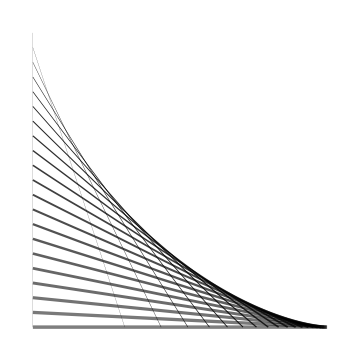

```mathematica
Graphics[Table[{AbsoluteThickness[x / 40],Opacity[(100-x/2) * 0.01],Line[{{0, 100 - x}, {Sqrt[100^2 - (100-x)^2], 0}}]}, {x, 0, 100, 5}], ImageSize -> Medium]
```

The coordinates of the corners of a regular n-gon are easy to calculate with some basic trigonometry. Here is a table of some n-gons for some reasonably small values of n. In the following expression, each Graphics object is a separate element of the list.

```mathematica
ngon[n_, r_] := Table[{r Cos[2π i/n], r Sin[2 π i / n]}, {i, 1, n+1}];
Table[Graphics[Line[ngon[i, 1]], ImageSize -> 80], {i, 5, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Internally, every graphical shape is still an expression, headed by the function symbol Line that gets a list of points as its argument and draws a sequence of line segments connecting them. We are never more than one application of FullForm to see this.

```mathematica
Line[ngon[3, 1]] // FullForm
```

Line[List[List[Rational[-1,2],Times[Rational[1,2],Power[3,Rational[1,2]]]],List[Rational[-1,2],Times[Rational[-1,2],Power[3,Rational[1,2]]]],List[1,0],List[Rational[-1,2],Times[Rational[1,2],Power[3,Rational[1,2]]]]]]

The function Line is actually twice misnamed. First, this function describes not really a line but a line segment (one would think that the mathematicians who created Mathematica would know this difference and at least feel some instinctive shudder for it), and second, like most of the graphics primitives in Mathematica, this function can define an arbitrary sequence of arbitrary sequences of connected line segments, not just one single line segment.

Tables, being expressions, can be nested inside each other to create lists of lists.

```mathematica
fgon[n_] := Table[Line[ngon[n, r]], {r, 0, 1, .1}];
Table[Graphics[fgon[i], ImageSize -> 80], {i,5, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Polygons and polyhedrons are so important that of course Mathematica comes with a vast knowledge base PolyhedronData of, well, all of them. To show the user results of computations that are lists that are way too long to show conveniently in their entirety, various views can be deployed. Each different type of view shows the user only one the elements at the time, along with some kind of control mechanism to choose the current element.

```mathematica
polygraphs = PolyhedronData["Archimedean", "NetGraph"];
Grid[{{TabView[polygraphs, ImageSize->Small], SlideView[polygraphs]},
{FlipView[polygraphs], PopupView[polygraphs]}}]
```

12345678910111213 | 
 |

As we saw at the end of the previous lesson, the massive knowledge bases of curated real world data in both Mathematica and Wolfram Alpha (just like the PolyhedronData knowledge base used in the previous example) typically give you lists of Entity expressions as results of the queries that you make. Each entity represents some real world concept outisde Mathematica along with its associated properties and their values. The values of the properties of that object can be extracted with the function EntityValue,  which is a hook to the Wolfram knowledge base, loading the latest data to the local kernel when necessary. These lists of entities can then be further massaged computationally like any other lists, so let us ask the CountryData knowledge base for the list of countries in South America for a nice little list that we can use to demonstrate the basic list processing functions.

```mathematica
sa = CountryData["SouthAmerica"]
Length[sa]
EntityValue[sa, "Population"]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,Falkland Islands,French Guiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

14

{41827217,10573218,201700544,17722868,48770570,15255149,2840,249408,760972,6913774,30418591,543497,3415252,30786062}

The elements of a list can be accessed with their indices starting from the first position, the indices starting from one and increasing all the way to the Length of the list. The indexing operation to access the element at the given position is denoted by duplicated square brackets, or you can equivalently use the function Part. To extract a longer sublist from inside another list, give the Part operator the start position and the end position separated by a double semicolon. Using an entire list as in index extracts the elements in the positions listed in the index, in the order that those positions appear. If some position is duplicated, that element will be duplicated correspondingly in the result.

```mathematica
sa[[3]]
sa[[5;;9]]
sa[[{5,8,2,2,3}]]
```

Brazil

{Colombia,Ecuador,Falkland Islands,French Guiana,Guyana}

{Colombia,French Guiana,Bolivia,Bolivia,Brazil}

The ability to extract the elements in the given positions that do not need to be sorted or unique can come handy in writing complex problems as one-liners when some other function can identify the positions where the desired elements are located inside the list, and the order in which they are intended to be extracted. For example, the list sa was originally sorted in alphabetical order by the names of the countries, but suppose we wish to find the first three countries sorted by population. The function Ordering returns the positions of the first k elements in the sorted order (or the last -k, if k is negative) using the provided comparison function between the elements. Compared to the straightforward approach of sorting the entire list and then just taking the sublist of the first k elements this has the advantage of being potentially much faster, since its internal quickselect algorithm does not need to care about or sort the remaining n - k elements once it has discovered which k elements are the smallest.

```mathematica
sa[[Ordering[sa,3, (EntityValue[#1, "Population"] > EntityValue[#2, "Population"])&]]]
```

{Brazil,Colombia,Argentina}

If the element itself is a list from which you wish to extract an element, you can do this one swoop by separating the nested positions with commas inside Part, or the equivalent double square brackets. This is just syntactic sugar for extracting the element inside the element in a sequential fashion.

```mathematica
hazards = EntityValue[sa,"NaturalHazards"];
hazards[[3]]
hazards[[3,2]]
hazards[[3]][[2]]
```

{drought,flood}

flood

flood

The convenience functions First, Last, Rest and Most give you convenient shorthands to extract specific parts of the list. These are often needed in many other functions that operate on lists, to avoid the clunky syntax for extracting sublists.

```mathematica
First[sa]
```

Argentina

```mathematica
Rest[sa]
```

{Bolivia,Brazil,Chile,Colombia,Ecuador,Falkland Islands,French Guiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
Most[sa]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,Falkland Islands,French Guiana,Guyana,Paraguay,Peru,Suriname,Uruguay}

The functions Rest and Most always produce a list as their answer, even when this answer contains only one element, which would happen when you apply these functions to some list that contains only two elements. When you apply these functions to a singleton list that contains only one element, the answer is an empty list, just like it ought to be. If applied to an empty list, the first element doesn’t exist and therefore the question of asking what elements follow it is nonsense to begin with, so the expression Rest[ { } ] does not simplify any further.

All of the previous functions can be used to take apart any expressions whatsoever, not just those that happen to be lists, that is, headed by the symbol List. The way that these functions work on arbitrary expressions just so happens to be very convenient for our purposes when we deal particularly with lists. In computing the positions where the arguments of a functions reside, remember that the expressions are not text strings but trees of subexpressions, built up by Mathematica under the guidance of precedence and associativity, and subject to sorting the arguments in the canonical order when the head of the expression has the attribute Orderless. For example, the operator Plus.

```mathematica
Part[a+b+c+d, 2]
Most[a+b+c+d]
Most[d+b*c+a]
```

b

a+b+c

a+b c

Table can be used to generate multidimensional lists of arbitrary depth, simply by using two or more loop counter variables with their own ranges. A two-dimensional list where all rows have the same number of columns is called a matrix. To display your nested list of lists as a proper matrix like it is done in the math class, you can use either MatrixForm or TableForm. The common operation of extracting a submatrix inside a larger matrix is best done with the function Take.

```mathematica
powerplus =Table[x^i + y^j, {i, 1, 5}, {j, 1, 4}];
powerplus // MatrixForm
Take[powerplus, {2,3},{1,3}] // MatrixForm
```

(x+y | x+y^2 | x+y^3 | x+y^4
x^2+y | x^2+y^2 | x^2+y^3 | x^2+y^4
x^3+y | x^3+y^2 | x^3+y^3 | x^3+y^4
x^4+y | x^4+y^2 | x^4+y^3 | x^4+y^4
x^5+y | x^5+y^2 | x^5+y^3 | x^5+y^4)

(x^2+y | x^2+y^2 | x^2+y^3
x^3+y | x^3+y^2 | x^3+y^3)

The order in which you define the loop counter variables is important. Compare the next expression to the previous one to see that the first variable becomes the outermost index, the second variable becomes the first nested index, and so on. This can be a bit counterintuive, as many people accustomed to the way that these kinds of definitions are read inside out would have reasonably expected this order to be the other way around.

```mathematica
MatrixForm[Table[x^i + y^j, {j, 1, 4}, {i, 1, 5}]]
```

(x+y | x^2+y | x^3+y | x^4+y | x^5+y
x+y^2 | x^2+y^2 | x^3+y^2 | x^4+y^2 | x^5+y^2
x+y^3 | x^2+y^3 | x^3+y^3 | x^4+y^3 | x^5+y^3
x+y^4 | x^2+y^4 | x^3+y^4 | x^4+y^4 | x^5+y^4)

Internally, all computers store characters as integers, so that possible integer value means some particular character. The functions ToCharacterCode and FromCharacterCode can be used to convert between numbers and characters. Here is a small sample of some more exotic characters from its vast character set, displayed using different font sizes and some garish colours to boot. Note the use of the function Style that can be wrapped around any expression, and whose options then can fine tune the control of how that expression is rendered.

```mathematica
cf2= ColorData["SolarColors"];
cf1 = ColorData["DeepSeaColors"];
TableForm[Table[Style[FromCharacterCode[RandomInteger[{100, 40000}]], FontSize -> (i+j+2)/2, FontColor -> cf1[RandomReal[]], Background -> cf2[RandomReal[]]], {i, 1, 20}, {j, 1, 20}], TableSpacing -> {0,0}]
```

帀 | ㆐ | 〵 | 䈓 | 䴈 | ㄷ | 裃 | ⣥ | 䯇 | 響 | 䮴 | 磯 | 蠜 | 耤 | ᖿ | 㧂 | ⹒ | 禲 | 藺 | 怬
ṷ | ᱈ | 筑 | 眝 | 䝒 | 峬 | 猍 | 蓺 | 血 | 鋹 | 嘆 | ᝞ | 鐥 | 玗 | 熆 | 洶 | 佯 | ⯀ | 氏 | 姜
綵 | 驫 | 邴 | 㢏 | Ï | 塒 | ᢺ | 㶊 | ྐྵ | 䎑 | 匋 | 㑞 | ࿯ | 㢁 | 浶 | 詺 | 粩 | 㓋 | 魁 | ᦮
偘 | 佱 | Օ | Ĵ | 㼫 | 㸗 | ៲ | 蓞 | 贌 | ⧸ | ⍜ | 帲 | 袜 | ஑ | 㧃 | 硔 | 咂 | 酿 | ↊ | 㨔
k | 悝 | 燽 | ᶯ | ᗱ | ⯬ | ⹜ | 訚 | ㈫ | 睏 | ㈸ | 炷 | 洿 | 䨂 | 纩 | 挬 | 嚤 | ⚬ | ᕫ | ࣱ
擾 | ኲ | 摍 | 指 | 洜 | 锅 | 媣 | 堲 | 笋 | ྜ | 㐥 | 宖 | 㸅 | 粑 | 锈 | ⿧ | 䡽 | 痮 | 緄 | ℋ
ᮋ | 䂪 | ή | 暌 | 缩 | 缝 | ව | 雿 | 㞙 | ✧ | ᪨ | Ꮝ | 绦 | 斛 | 䗻 | 魟 | 䰯 | ⭜ | 蓗 | ᙸ
柜 | ž | 程 | 蚶 | 蠡 | 冦 | 堐 | 薀 | 誀 | ㊃ | 铮 | 髁 | ᔻ | 叕 | 嵞 | 棚 | 隕 | ⵊ | 㠐 | 㫈
骉 | 牮 | 玂 | 㗜 | 橒 | 欅 | 貯 | 靅 | ∪ | ⯘ | 唱 | 㰁 | ྠ | 䙹 | 禷 | 廼 | 孏 | ⑎ | ⽙ | 嫎
芮 | ⴈ | ዋ | 湳 | ⭵ | ㎰ | ⾒ | 睤 | 㡢 | ず | 䀠 | 騼 | 䫼 | 篥 | 緧 | ┺ | ւ | 欳 | 㖠 | 机
༧ | 䳀 | 胬 | 䉜 | ⺨ | 饻 | ᴽ | ׹ | ǧ | 陴 | ⬤ | 枏 | 譥 | 錤 | ⅷ | ➱ | 䂅 | ㋄ | ೆ | 砬
夋 | 輝 | ޓ | ၳ | ㆽ | 䇗 | 谯 | Ẵ | ざ | ᱞ | ⺐ | ䷢ | 醷 | 䇸 | ུ | 颹 | ᕓ | ⧙ | 䎎 | ৒
⽑ | 㩞 | 韓 | 䓌 | 碭 | 綕 | ⑇ | 赉 | 舷 | 詰 | ॗ | ᘠ | 攐 | 㚺 | 怀 | ॅ | 伎 | ䷅ | Ȣ | ᤒ
䎣 | 諙 | 类 | ᾽ | 㫎 | 䀱 | 迸 | 軺 | 㣄 | 䔒 | 抧 | 㠿 | 竺 | ৾ | 斬 | ԉ | 奸 | ₤ | ヱ | ᜔
㮄 | ⁄ | Ƴ | ⽄ | ⦵ | 剶 | 㰬 | 絞 | 硚 | ☪ | 譸 | 抓 | 鎫 | ۢ | ໽ | ᘛ | 糠 | 廚 | 寞 | ൨
锋 | 㧹 | ⎭ | ⳬ | ⏻ | ቙ | 勓 | 㔖 | 之 | 簖 | 痞 | Ქ | ⚳ | ㋚ | ⢀ | 䶵 | 橇 | ␪ | 媕 | 睫
⪈ | 㴜 | 蚉 | 僅 | 铈 | 燌 | 䉸 | ⠡ | 艽 | ⢞ | 瑛 | 蹇 | Ở | 諴 | ⤦ | 礟 | 䵤 | ׁ | 䮐 | 牛
⣯ | 綼 | ⦏ | 䕧 | ᗖ | ㆬ | 㘔 | Ѵ | ㇔ | 喵 | 䕚 | 䝘 | ⁽ | 㥉 | 鯴 | ཥ | ↵ | 輼 | 瘪 | Ờ
䈩 | 开 | อ | 蘩 | 葻 | 乏 | 䍒 | ࠁ | 諕 | 驗 | Ἡ | 㸪 | 欣 | 歝 | 醅 | ൰ | 営 | Ǒ | 渉 | 悌
恟 | 䳃 | ║ | 腬 | 姨 | ᆡ | 睁 | 䍗 | ⁕ | 謳 | ጚ | ᏾ | 壮 | ∳ | ࠽ | 匯 | 许 | 嚄 | 䞇 | 扬

When shown in TableForm, the columns and rows of the table can be given descriptive headings. Consider the table that plots some functions that often occur in the analysis of the running times of the algorithms. If the running time of some algorithm, expressed as a function of the input size n, is proportional to the function in the column, the table shows how the running time will grow along with the input size. The table shows how for large n, the running time of two algorithms for the same problem can easily differ by orders of magnitude. On the other hand, algorithms whose running time is only logarithmic can handle even large problems without breaking a sweat. In practice, the most important gap in algorithm running times is the one that separates the linear time algorithms from those that operate in quadratic time. In practice, cubic time is the highest order of polynomial that we ever encounter in the analysis of running times of algorithms for real problems. Once the algorithm gets past that threshold, the running time of that algorithm will more often than not turn out to be some sort of exponential. Exponential-time algorithms will simply not be feasible to solve except for very small n. Many exponential time algorithms might work out to be polynomial for the majority of their possible instances, but they can surprise you by falling into a seemingly endless computation that would not end during our lifetimes.

```mathematica
funcs ={Log[n], n, n Log[n], n^2, n^3, 2^n};
args = Table[10^i, {i, 1, 6}];
times = Table[N[f /. n-> v,3], {v, args},{f, funcs} ];
TableForm[times, TableHeadings -> {args, funcs}]
```

| Log[n] | n | n Log[n] | n^2 | n^3 | 2^n
10 | 2.3 | 10. | 23. | 100. | 1000. | 1020.
100 | 4.61 | 100. | 461. | 10000. | 1.×10^6 | 1.27×10^30
1000 | 6.91 | 1000. | 6910. | 1.×10^6 | 1.×10^9 | 1.07×10^301
10000 | 9.21 | 10000. | 92100. | 1.×10^8 | 1.×10^12 | 2.×10^3010
100000 | 11.5 | 100000. | 1.15×10^6 | 1.×10^10 | 1.×10^15 | 9.99×10^30102
1000000 | 13.8 | 1.×10^6 | 1.38×10^7 | 1.×10^12 | 1.×10^18 | 9.9×10^301029

In a multidimensional table, the rows don’t need to be all the same length, but then the result will not be a proper matrix, but a plain old list of lists. We can still display it as a table, though, using the same function TableForm that does the right thing even with such ragged lists.

```mathematica
Table[x^i + y^j, {i, 1, 5}, {j, 1, i}] // TableForm
```

x+y |  |  |  | 
x^2+y | x^2+y^2 |  |  | 
x^3+y | x^3+y^2 | x^3+y^3 |  | 
x^4+y | x^4+y^2 | x^4+y^3 | x^4+y^4 | 
x^5+y | x^5+y^2 | x^5+y^3 | x^5+y^4 | x^5+y^5

One last snazzy example of using Table, inspired by the “Boids” swarm intelligence simulation. The original boids are simulated birdoids that move across space so that they they try to maintain at least a minimum distance to their neighbours while also trying to move towards the center of the flock. From these simple local rules, a surprisingly natural-looking flocking behaviour emerges globally from the self-organization of the system from these local rules without any kind of a global control needed to achieve this. The following function implements a variation where each boid has one friend and one enemy, randomly chosen by permuting the list of boids, so that the boid accelerates towards its friends and away from its enemy. So that the boids won’t just all shoot towards infinity, each boid also accelerates towards the origin of the coordinate system, to keep the flock together. The following implementation, implemented as a Module to allow its names and rules to be local variables inside the module body, internally uses memoization to  calculate and store the position and velocity x[t] and v[t] of each boid at the discrete time steps. These positions are then drawn using a BSplineCurve instead of Line to smoothly interpolate the intermediate points. The shape of the curves is determined by the randomly chosen initial positions of the boids and their friends and enemies.

```mathematica
boidcurve[boids_, tmax_] := Module[{friends, enemies, x, v},
friends = RandomSample[Range[1, boids], boids];
enemies = RandomSample[Range[1,boids],boids];
x[0] = RandomReal[{-1, +1}, {boids, 2}];
v[0] = RandomReal[{-1, +1}, {boids, 2}];
x[t_] := x[t] = x[t-1] + 0.01 v[t-1];
v[t_] := v[t] = v[t-1] + Permute[x[t-1], friends] - Permute[x[t-1], enemies] -30 x[t-1];
Graphics[Table[{RGBColor[{RandomReal[], RandomReal[],  RandomReal[]}],BSplineCurve[Table[x[t][[i]], {t, 0, tmax}]]} ,{i, 1, boids}]]
];

GraphicsGrid[Table[boidcurve[3+5*i+j, 300], {i, 0,3}, {j, 0,4}]]
```

-Graphics-

The function Permute used in the previous example takes a list and produces a new list where each element ends up in the position given by the second argument list. Some other built-in generators for more complicated forms of lists that will come handy in various little combinatorial algorithms include functions to generate all tuples, subsets and permutations of some already existing list.

```mathematica
Tuples[{a, b, c}, 3]
```

{{a,a,a},{a,a,b},{a,a,c},{a,b,a},{a,b,b},{a,b,c},{a,c,a},{a,c,b},{a,c,c},{b,a,a},{b,a,b},{b,a,c},{b,b,a},{b,b,b},{b,b,c},{b,c,a},{b,c,b},{b,c,c},{c,a,a},{c,a,b},{c,a,c},{c,b,a},{c,b,b},{c,b,c},{c,c,a},{c,c,b},{c,c,c}}

```mathematica
Permutations[{a, b, c, d}, {3}]
```

{{a,b,c},{a,b,d},{a,c,b},{a,c,d},{a,d,b},{a,d,c},{b,a,c},{b,a,d},{b,c,a},{b,c,d},{b,d,a},{b,d,c},{c,a,b},{c,a,d},{c,b,a},{c,b,d},{c,d,a},{c,d,b},{d,a,b},{d,a,c},{d,b,a},{d,b,c},{d,c,a},{d,c,b}}

```mathematica
Subsets[{a, b, c, d}]
```

{{},{a},{b},{c},{d},{a,b},{a,c},{a,d},{b,c},{b,d},{c,d},{a,b,c},{a,b,d},{a,c,d},{b,c,d},{a,b,c,d}}

The function Tuples can often do the job usually done with nested for-loops of imperative programming languages to iterate through all possible pairs of elements inside the list. Tuples also has an alternative form where the elements of each tuple are drawn all possible ways not from the same list, but each component of the tuple is drawn from the corresponding argument list. As an example of this technique, create a list containing all 52 cards in the normal deck, each card a list containing the suit and rank of that card. To type in the suit symbols and other special characters, type a backslash and a pair of square brackets that contain the name of the special character (e.g. HeartSuit) inside them, and the front end automatically turns this mess into that special symbol.

```mathematica
Tuples[{ { ♢,♣,♡,♠}, {"A",2,3,4,5,6,7,8,9,10,"J","Q","K"}}]
```

{{♢,A},{♢,2},{♢,3},{♢,4},{♢,5},{♢,6},{♢,7},{♢,8},{♢,9},{♢,10},{♢,J},{♢,Q},{♢,K},{♣,A},{♣,2},{♣,3},{♣,4},{♣,5},{♣,6},{♣,7},{♣,8},{♣,9},{♣,10},{♣,J},{♣,Q},{♣,K},{♡,A},{♡,2},{♡,3},{♡,4},{♡,5},{♡,6},{♡,7},{♡,8},{♡,9},{♡,10},{♡,J},{♡,Q},{♡,K},{♠,A},{♠,2},{♠,3},{♠,4},{♠,5},{♠,6},{♠,7},{♠,8},{♠,9},{♠,10},{♠,J},{♠,Q},{♠,K}}

Once the lists have been generated, it is time to perform actual computations on them.  With the function Subsets available, we have a concise way to solve the subset sum problem: given a list of elements, typically positive integers, does there exist a subset of it whose elements add up exactly to the given goal?

```mathematica
subsetsum[li_, goal_] := AnyTrue[Subsets[li],(Total[#] == goal)&];
subsetsum[{5, 8, 12, 13, 16, 21, 33}, 64]
```

False

This function works in principle but would be highly inefficient in memory use for large lists, because it will explicitly construct all of its possible subsets, of which there are exponentially many. (In combinatorics, basically there is always an exponential number of ways that n items can be arranged under the given constraints.) It also seems quite silly to generate all subsets before checking any of them for the answer, if the very first subset generated would be the correct answer! We will later see more efficient ways to solve this problem, although the running time of these techniques will still be inherently exponential, since the subset sum problem is one of the many NP-complete decision problems, for which only exponential time algorithms are known.

Intuitively, all of these NP-complete problems are disguises for searching for a small needle in a haystack whose size is exponentially large. By far the most important unsolved problem in computer science is to determine whether there can exist efficient algorithms for these NP-complete problems. However, even if this turned out not to be the case, as most experts agree is probably the case, there still exists a spectrum of variations in these problems about how quickly they can be solved on average. Even though the haystack is exponentially large, as long there exists an exponential number of needles in it and you only have to find any single one of them, your searching time will probably be short on average, as turns out to be the case for randomly generated instances of the subset sum.

The functions AnyTrue, NoneTrue and AllTrue can be used to check whether the elements of some list have some desired or undesired property universally or existentially. For example, given the prime factorization of an integer along with the powers of each prime factor, we can determine whether it is squarefree, that is, its prime factorization does not contain any second powers of some prime factor.

```mathematica
squarefree[n_] := AllTrue[FactorInteger[n], (#[[2]] < 2)&];
squarefree[Apply[Times, Table[Prime[i],{i,1,100}]]]
squarefree[2*3*5*5*7*11]
```

True

False

## Map and its variations

The important function Map is used to apply the function given to it as first argument separately to every element of the list given as second argument, producing a new list for these results that is exactly the same Length as the original. The following example computes the square roots of the first ten positive integers. The shorthand /@ is often seen in other people’s Mathematica code, so it is good to be able to recognize this symbol even if you don’t use it yourself. (To recap: @* is shorthand for Composition, /@ is shorthand for Map, /. is shorthand for Replace and @@ is shorthand for Apply.)

```mathematica
Map[Sqrt, Range[10]]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

```mathematica
Sqrt /@ Range[10]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

The job of Map can occasionally be done equally well by application of a substitution rule with pattern marching.

```mathematica
Range[10] /. x_ -> Sqrt[x]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

Map can be combined with recursion for powerful symbolic computations that operate and modify the structure of an arbitrary expression. For example, here is a recursive function that counts how many leaf nodes there are in the tree form of its argument expression. The function Length is used to check whether the expression is itself a leaf, and otherwise the number of leaves in the entire expression equals the sum of the recursively computed numbers of leaves of its subexpressions.

6

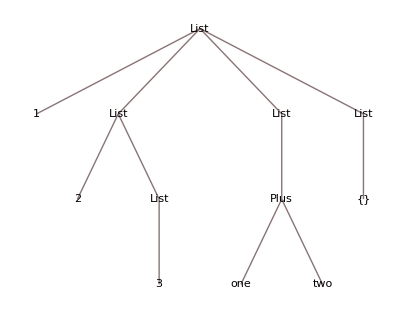

```mathematica
countleaves[exp_] :=
If[Length[exp] == 0,
1,
Total[Map[countleaves[exp[[#]]]&, Range[1, Length[exp]]]]
];

countleaves[{1, {2, {3}}, {one + two}, {{}}}]
TreeForm[{1, {2, {3}}, {one +two}, {{}}}]
```

With the same principle, we can write a function frameleaves that constructs an expression otherwise identical to its argument, but each leaf node of the tree form has been doubly Framed.

```mathematica
frameleaves[exp_] :=
If[Length[exp] == 0,
Framed[Framed[exp, RoundingRadius -> 4 ],  RoundingRadius -> 6],
Apply[Head[exp], Map[frameleaves[exp[[#]]]&,Range[1, Length[exp]]]]
];

frameleaves[{1, {2, {3}}, {one + two}, {{}}}]
```

{1,{2,{3}},{one+two},{{}}}

Strange things can happen when functions get applied to themselves. Again, everything is a symbolic expression.

```mathematica
frameleaves[2]
frameleaves[frameleaves[2]]
frameleaves[frameleaves[frameleaves[2]]]
```

2

Framed[Framed[2,RoundingRadius→4],RoundingRadius→6]

Framed[Framed[Framed[Framed[2,RoundingRadius→4],RoundingRadius→6],Framed[Framed[RoundingRadius,RoundingRadius→4],RoundingRadius→6]→Framed[Framed[4,RoundingRadius→4],RoundingRadius→6]],Framed[Framed[RoundingRadius,RoundingRadius→4],RoundingRadius→6]→Framed[Framed[6,RoundingRadius→4],RoundingRadius→6]]

As an aside, the four symbols foo, bar, baz and qux, often seen in this sort of examples, are the canonical placeholder names used in computer science in situations where some name is needed to illustrate the abstract concept but that actual name and especially what it refers to are irrelevant. When seeing these symbols being used, the reader is expected automatically benevolently understand that this particular name is meaningless and should not waste time searching for and pondering any deeper meanings for these names. These canonical placeholder names are not symbols of the programming language, but metasymbols that are used to talk about the actual symbols of the programming language. Naming an actual variable in a real working program using a metasymbolic placeholder name would always be a very silly thing to do. In situations where you need some integer value to illustrate some function that needs an integer argument, the values 17, 42 and 99 appearing as magic numbers without any explanatory context are canonically understood to be meaningless numbers generated with the proverbial “Stetson method”, that is, pulled out of the hat.

Similar placeholder names appear in many other more familiar walks of life, such as using the names Alice, Bob, Carol and Dave in puzzles where some people have to cross a river with a boat that can carry two people at the time, and the reader tacitly understands that the actual names and identities of these people are irrelevant for the puzzle at hand, but we just need to have some names to be able to talk about these imaginary people in the first place. (If there is only one person, he or she would be called John or Jane Doe, two people might be called Moe and Joe, three people might be Tom, Dick and Harry, and so on.)

One more example in the same vein, a function shuffleexp that rearranges the branches of its expression tree into a random order, recursively shuffling the branches of each subexpression.

```mathematica
shuffleexp[exp_] :=
If[Length[exp] == 0,
exp,
Apply[Head[exp], RandomSample[Map[shuffleexp[exp[[#]]]&, Range[1, Length[exp]]]]]
]
shuffleexp[{1,2,{3, foo[bar, baz, quz]},4}]
```

{{3,foo[bar,baz,quz]},4,2,1}

The next example uses the built-in function Tally that counts how many times each unique element occurs in a list, producing a list of unique elements paired with their occurrence counts.

```mathematica
Tally[{1, 4, -3, -3, 5, 4, 4, 1, 1, -3, 5}]
```

{{1,3},{4,3},{-3,3},{5,2}}

In the card game of badugi that is played like draw poker, each player initially receives four cards, and the play of the hand consists of four rounds of betting and three rounds of drawing interleaved together. Each player who pushes enough chips to the pot to stay in tries to draw a hand where no rank or suit is duplicated, the best such hand (measured by the smallest high card, breaking the ties by the second highest card, and so on) scooping the pot. If some player doesn’t draw any cards in the first drawing round, presenting having been dealt a pat badugi, what are the a priori frequencies for each rank for the highest card in his badugi? To answer this question, we generate all possible 4-card subsets of the 13 ranks of playing cards, map each subset to its highest card, and tally how many times each highest card occurs in the resulting list.

```mathematica
Tally[Map[Max[#]&,Subsets[Range[1, 13], {4}]] /. {x_, y_} -> y]
```

{{4,1},{5,4},{6,10},{7,20},{8,35},{9,56},{10,84},{11,120},{12,165},{13,220}}

As the result list shows, a pat badugi dealt to the player is 220 times more likely to be a king-high than a 4-high, the best possible badugi hand and the counterpart of the royal flush of regular poker. Even assuming that the opponent is not “snowing”, drawing against a badugi that was dealt as a pat badugi is usually a good proposition. Drawing against a badugi that is made after one or two draws is a completely different story, as the conditional probabilities and the Nash equilibria in that situation are very much different than those determined by the initial fair random shuffle of the deck.

The next example uses Map to first calculate the population densities of the countries in South America, and then sort these countries according to their population density.  Whenever you have entities that contain many things inside them, Map can be used to project those entities to lists of only those things that you care about. In this particular problem we care only about name, population and area of those countries, but not the GDP, the national anthem, average rainfall, the colours of the flag, or any other of the myriad aspects that make up a nation. (In some other problem in which we care about those things, we would then project differently according to the needs of that problem.)

```mathematica
Map[{CountryData[#, "Name"],CountryData[#, "Population"] / CountryData[#, "Area"]}&, CountryData["SouthAmerica"]];
Sort[%, (Last[#1] > Last[#2])&] // TableForm
```

Ecuador | 53.7985
Colombia | 42.8221
Venezuela | 33.7548
Brazil | 23.688
Peru | 23.6681
Chile | 23.4398
Uruguay | 19.3812
Paraguay | 16.9975
Argentina | 15.1171
Bolivia | 9.62443
Guyana | 3.53992
Suriname | 3.31765
French Guiana | 2.74075
Falkland Islands | 0.233303

Note how the symbolic units people and km automatically tag along the symbolic computations, even if the pattern matching engine doesn’t have a clue about what these units mean. As an aside, according to the late great computer scientist Edsger W. Dijkstra, computer science is not a real science as long as we keep using anthropomorphic terms (such as “doesn’t have a clue” in the previous sentence) to talk about the behaviour of computer programs. However, we can counter this by noting that when talking about a behaviour of some system that is far too complex to explain on physical or design level, which would encompass basically any computer program, it is far more convenient to take an intentional stance and assign beliefs, desires and intentions to this system as convenient shorthands used to predict and explain its behaviour, even if we don’t actually believe that a computer program is “thinking” in the sense of Strong AI. After all, the two stances “it really is X” and “it behaves as if it were X” always produce the exact same predictions about the externally observable behaviour of any system. And with computer programs, the external behaviour as mapping from inputs the outputs is what matters, and as long as the program does that correctly, it should not matter even if there is a three ring circus inside the black box of computation.

The curated geographical data about every country and their administrative regions even includes the polygon of its natinal borders, naturally given in correct geometric (heh) position coordinates so that when rendered in the same coordinate system, these polygons fit together snugly just like they fit on the surface of actual Earth. To make the individual countries visible, we are going to use different colours, as otherwise we would end up with only the flat solid shape of the entire continent without the distinction of borders. To create random colours for entities of your graphics, it is usually a good idea to use some existing colour function to generate the random colours from some aesthetic looking palette of colours that play well together.

```mathematica
With[{cf = ColorData["Rainbow"]},Graphics[Map[({cf[RandomReal[]],CountryData[#, "Polygon"]})&, CountryData["Africa"]], ImageSize -> Small]]
```

-Graphics-

Our next example plays around with some rudimentary linguistics. Considering the words of the English language that start with the prefix “ram”, what is their length distribution? (The string expression that consists of three underscores matches zero or more occurrences of any character, and the double tilde operator combines two string patterns. The double tilde operator ~~ can be used to concatenate arbitrary string expressions to create a pattern to match strings against.)

```mathematica
ramwords = DictionaryLookup["ram" ~~ ___]
```

{ram,ramble,rambled,rambler,ramblers,rambles,rambling,ramblings,rambunctious,rambunctiously,rambunctiousness,ramekin,ramekins,ramie,ramification,ramifications,ramified,ramifies,ramify,ramifying,ramjet,ramjets,rammed,ramming,ramp,rampage,rampaged,rampages,rampaging,rampancy,rampant,rampantly,rampart,ramparts,ramped,ramps,ramrod,ramrodded,ramrodding,ramrods,rams,ramshackle}

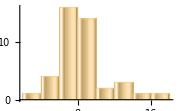

```mathematica
Histogram[StringLength[ramwords], ChartElementFunction -> "GlassRectangle", ImageSize -> Small]
```

In Mathematica, basically every important list processing function Foo has its string processing counterpart named StringFoo. In the previous example, it is important to use the function StringLength instead of Length. The same holds for other string processing counterparts of the list functions. Because the string versions of these functions are supposed to operate on strings, they are defined to be Listable so that given a list of strings, they produce the list of results of applying that function to each element.

Surely more people are already familar with regular expressions than they are of Mathematica string expressions. Fortunately RegularExpression can convert any regular expression into a string expression.

```mathematica
Length["Hello world"]
StringSplit["Hello there, world!"]
StringCases["supercalifragilisticexpialidocious", RegularExpression["[aeiou]{2}"]]
StringCount["supercalifragilisticexpialidocious", RegularExpression["[aeiou]"]]
StringPosition["supercalifragilisticexpialidocious", RegularExpression["[aeiou]"]]
StringReplace["Hello there, world!", "o" -> "bob"]
```

0

{Hello,there,,world!}

{ia,io}

16

{{2,2},{4,4},{7,7},{9,9},{12,12},{14,14},{16,16},{19,19},{21,21},{24,24},{25,25},{27,27},{29,29},{31,31},{32,32},{33,33}}

Hellbob there, wbobrld!

All these list processing functions can be combined in many ways to do the same operation in many different ways. For example, given a list of points on the two-dimensional plane, we wish to extract their x- and y-coordinates to two separate lists. Either Map, substitution rules or matrix Transpose do the job nicely.

```mathematica
points = {{1, 3}, {-2, 4}, {8, 5}, {3, -4}, {-5, 0} };
{ Map[(First[#])&, points], Map[(First[Rest[#]])&, points] }
{ points /. {x_, y_} -> x, points /. {x_, y_} -> y }
Transpose[points]
```

{{1,-2,8,3,-5},{3,4,5,-4,0}}

{{1,-2,8,3,-5},{3,4,5,-4,0}}

{{1,-2,8,3,-5},{3,4,5,-4,0}}

The function Apply can be used to an arbitrary expressions, including lists, to change its head to something else. Its shorthand form, often seen in other people’s example code, is @@, for those who prefer to use the more terse syntax. If you want to change the heads of all elements inside a list, you can Map the function Apply to the elements of that list.

```mathematica
Map[(Apply[f, #])&, { {1, 2,3}, {a, b, c}, {x, x^2, x^10, x^100} }]
```

{f[1,2,3],f[a,b,c],f[x,x^2,x^10,x^100]}

```mathematica
Map[(f @@ #)&, { {1, 2,3}, {a, b, c}, {x, x^2, x^10, x^100} }]
```

{f[1,2,3],f[a,b,c],f[x,x^2,x^10,x^100]}

Alternatively, functions such as Map, Apply and Flatten can be given a level specification parameter that determines what depth they are supposed to operate on the given list. The default level specification of Map and Apply is {1} to restrict the operation to the first level only, whereas the default level specification of Flatten is Infinity. However, you need to be careful using this technique not to unintentionally change the head of some compound expression.

```mathematica
Apply[f,  { {1, 2,3}, {a, b, c}, {x, x^2, x^10, x^100} }, {2}]
```

{{1,2,3},{a,b,c},{x,f[x,2],f[x,10],f[x,100]}}

Apply can usually do the job of the outer loop in problems such as adding up all the elements of the list. The pattern matching rules for expression simplification do the rest.

```mathematica
harmfact[n_] := Plus @@ Table[1/i!, {i, 1, n}];
harmfact[7]
```

433/252

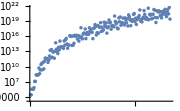

```mathematica
ListLogPlot[Table[LCM @@ Table[j, {j, i, i+10}], {i, 1, 200}], ImageSize -> Small]
```

Sky is the limit for what the function that you map over the elements could be. For example, Map itself is a function. Therefore, to apply some function to each element of each list, simply Map a Map.

```mathematica
Map[(Map[f, #])&, { {1, 2,3}, {a, b, c}, {x, x^2, x^10, x^100} }]
```

{{f[1],f[2],f[3]},{f[a],f[b],f[c]},{f[x],f[x^2],f[x^10],f[x^100]}}

The next example uses a Map to generate a list of 500 triples of random decimal numbers, which are then mapped to a list of Cuboid objects, which are then mapped to Rotate a random angle around the vector {0, 0, 1} (that is, around the Z-axis). This list of cuboids is then rendered into a Graphics3D object, using partially transparent colouring so that you can see the cuboids that are fully or partially covered by the other cuboids in front of them.

```mathematica
cf = ColorData["Rainbow"];
Graphics3D[{Opacity[.6],
  Map[{cf[RandomReal[]],(Rotate[#, RandomReal[π], {0,0,1}])}&, Map[Cuboid, RandomReal[{-5, 5}, {500, 3}]]]
}, Boxed-> False, Background -> Black, ViewAngle -> 20 Degree
]
```

-Graphics3D-

The variation MapThread can be used to riffle together two or more lists of the same length, applying its first argument function to the elements in the corresponding location.

```mathematica
MapThread[Plus, {{1, 2, 3}, {bob, tom, jim}, {a, b, c}}]
```

{1+a+bob,2+b+tom,3+c+jim}

Suppose you have a list of randomly chosen center points, and another separate list of their randomly chosen radii. MapThread can then be used to combine these two lists into balls.

```mathematica
centers = RandomReal[{-2, +2}, {100, 3}];
radii = Abs[RandomVariate[NormalDistribution[.3,.1], 100]] + .1;
Image[Graphics3D[{Opacity[0.3], MapThread[Ball, {centers, radii}]}, Boxed-> False,Background -> White]]
```

-Graphics-

Yet another variation MapIndexed applies a function that takes to parameters to each element with its position index. This way, the computation done for each element can depend on its position in addition to its value.

```mathematica
MapIndexed[(Table[#1, {i, 1, First[#2]}])&,{one, two, three, four}]
```

{{one},{two,two},{three,three,three},{four,four,four,four}}

Riffle is an alternative to MapThread that, just like it says on the tin, can be used to riffle together the elements of its argument lists, not necessarily of the same length, when you don’t need to combine the elements together using some function but want to keep them separate. In the common case where both lists have the same length, this operation corresponds to one round of riffle shuffle of a deck of cards, hence the name. But this operation generalizes for arbitrary lengths of its argument lists, the function taking elements from lists in an alternating fashion and looping back to the beginning of each list whenever it runs past its end.

```mathematica
Riffle[Table[i^2, {i, 1, 10}], {bob, tom, jim}]
```

{1,bob,4,tom,9,jim,16,bob,25,tom,36,jim,49,bob,64,tom,81,jim,100}

For the final example of this section, let us investigate how the famous Benford’s law applies to data taken from both the real world and abstract mathematics. Benford’s law is a famous observation that the first digits of numerical values extracted from a dataset are not uniformly distributed, but that the digit d appears with probability Log10[ (d + 1) / d ] so that small digits are more probable than large digits. As the real world data set, let us use the mountains of the world, at least those that are known by the Wolfram knowledgebase as mountains.

```mathematica
mountains = MountainData[];
Length[mountains]
RandomSample[mountains,10]
```

14879

{Mount Tullu Dimtu,Stoppelberg,Sant Amand,Jabal Hafarah,Knogl,Pen Hill,Chullpa,Rose Peak,Overhanging Tower,Hollybush Hill}

The almost fifteen thousand entities that comprise this list hopefully have their elevation expressed in meters, but just in case somebody snuck something else inside that list, the handy function UnitConvert will perform the necessary conversion. Even so, to demonstrate that the conformance to the Benford’s law is not merely an artifact of our metric system, we will do the same computation separately in meters, feet and fathoms, as computed by the function allUnits. Since the knowledge base can contain Missing values, we have to write the conversion rule to treat such missing values as zeros, since that is the best that we can possibly do here without starting some kind of guesstimation. (On the other hand, it might not actually be that difficult to look up the mountains in WikipediaData and extract the answer from there... something to think about.)

```mathematica
mountainHeights = UnitConvert[EntityValue[mountains, "Elevation"], "Meters"];
allUnits[Missing[_]] := {0,0,0};
allUnits[h_] := With[{hh = First[h]},{hh, 3.28084*hh,0.546807*hh}];
```

Mathematica built-in functions IntegerDigits and RealDigits can easily extract the digits from inside a number. We need to write a rule for both possibilities here, since the knowledge base of mountains contains values encoded in both ways.

```mathematica
firstDigit[v_Real] := First[First[RealDigits[v]]];
firstDigit[v_Integer] := First[IntegerDigits[v]];
firstDigit[v_List] := Map[firstDigit, v];
extractDigits[list_] := Map[firstDigit,Map[allUnits,list],{1}];
```

The function benfordCount computes the proportion of occurrences of each digit from one to nine as the first digit of the numbers given inside its parameter list. Since we are doing the same computation separately for three separate units of measurement, with the same mountain elevations in these three units given as the rows of the two-dimensional matrix, we have to transpose this matrix so that these rows become columns for the purposes of the Benford calculation.

```mathematica
ClearAll[benfordCount]
benfordCount[values_] := Table[Count[values, d] / Length[values], {d, 1, 9}]; 
TableForm[Transpose[N[Join[Map[benfordCount,Transpose[extractDigits[mountainHeights]]], {Table[Log10[(d+1)/d],{d,1,9}]}],3]],TableHeadings->{Range[1,9],{"Meters","Feet", "Fathoms", "Predicted"}}]
```

| Meters | Feet | Fathoms | Predicted
1 | 0.216 | 0.369 | 0.415 | 0.301
2 | 0.247 | 0.128 | 0.212 | 0.176
3 | 0.172 | 0.0796 | 0.104 | 0.125
4 | 0.102 | 0.0615 | 0.0621 | 0.0969
5 | 0.103 | 0.0657 | 0.0503 | 0.0792
6 | 0.0554 | 0.0668 | 0.0436 | 0.0669
7 | 0.0443 | 0.0719 | 0.036 | 0.058
8 | 0.0305 | 0.0766 | 0.037 | 0.0512
9 | 0.0292 | 0.08 | 0.04 | 0.0458

The general shape of the proportions seems all right in all three units of measurement. Perhaps some purely mathematical data would fit the Benford’s law better... how about the first digits of the factorials of the first five thousand integers, or the powers of two and three? Amazingly, those happen to fit the prediction of the Benford’s law like a glove! The powers of ten, on the other hand, for obvious reasons, fail the Benford test miserably. (Could you think up a general rule to identify the bases whose powers the Benford’s law works out?)

```mathematica
TableForm[N[Transpose[{benfordCount[Map[firstDigit,Table[Factorial[i],{i,1,5000}]]],
benfordCount[Map[firstDigit,Table[2^i,{i,1,5000}]]],benfordCount[Map[firstDigit,Table[3^i,{i,1,5000}]]],
benfordCount[Map[firstDigit,Table[10^i,{i,1,5000}]]],
Table[Log10[(d+1)/d],{d,1,9}]}],3], TableHeadings->{Range[1,9], {n!,2^n ,3^n,10^n,"Predicted"}}]
```

| n! | 2^n | 3^n | 10^n | Predicted
1 | 0.298 | 0.301 | 0.301 | 1. | 0.301
2 | 0.178 | 0.176 | 0.176 | 0 | 0.176
3 | 0.121 | 0.125 | 0.125 | 0 | 0.125
4 | 0.0954 | 0.097 | 0.097 | 0 | 0.0969
5 | 0.0792 | 0.0794 | 0.0792 | 0 | 0.0792
6 | 0.0774 | 0.067 | 0.067 | 0 | 0.0669
7 | 0.0564 | 0.0576 | 0.058 | 0 | 0.058
8 | 0.051 | 0.0518 | 0.0514 | 0 | 0.0512
9 | 0.043 | 0.0452 | 0.0458 | 0 | 0.0458

## Selecting and tallying elements of a list

The function Select inspects its argument list element by element to generate the result list that contains only those original elements for which the criterion function given as its second argument evaluates to True. For example, we can select all the palindromes from the list of words in the Swedish dictionary.

```mathematica
Select[DictionaryLookup[{"Swedish", All}], (# == StringReverse[#])&]
```

{å,aga,alla,amma,ana,apa,dåd,dammad,död,ene,esse,girig,i,kajak,kok,kök,madam,nån,ö,oro,pep,pip,pop,radar,rakar,ramar,rar,rår,rasar,rattar,reder,reser,ror,rör,rosor,sagas,sas,sås,ses,snarans,snöns,stannats,stats,stegets,stöts,sus,sys,talat,tappat,tassat,tät,teet,tennet,tet,tigit,tillit,varav,väv,vev,viv}

Generate the first one thousand Fibonacci numbers, but leave in only those that are also happen to be prime numbers. This function Select can therefore be used to filter out the undesirable elements from any list that we have previously generated. The elements in that sequence get pretty big pretty fast.

```mathematica
Select[Table[Fibonacci[i], {i, 1, 1000}], PrimeQ]
```

{2,3,5,13,89,233,1597,28657,514229,433494437,2971215073,99194853094755497,1066340417491710595814572169,19134702400093278081449423917,475420437734698220747368027166749382927701417016557193662268716376935476241,529892711006095621792039556787784670197112759029534506620905162834769955134424689676262369,1387277127804783827114186103186246392258450358171783690079918032136025225954602593712568353,3061719992484545030554313848083717208111285432353738497131674799321571238149015933442805665949,10597999265301490732599643671505003412515860435409421932560009680142974347195483140293254396195769876129909,36684474316080978061473613646275630451100586901195229815270242868417768061193560857904335017879540515228143777781065869,96041200618922553823942883360924865026104917411877067816822264789029014378308478864192589084185254331637646183008074629}

The earlier function squarefree could alternatively be implemented using Select.

```mathematica
squarefree[n_] := Length[Select[FactorInteger[n], (#[[2]] > 1)&]] == 0;
squarefree[2*5*7]
squarefree[2*3*5*7*5]
```

True

False

Considering only the words that consist of four or more characters, what are the twenty most frequent words in Alice in Wonderland? Regular expressions to break the text into the list of its individual words, using the regular expression \W+ of one or more nonword characters as the separator for StringSplit, followed by Tally to then count the occurrences of each word, make short work of this problem. Again, the function Ordering is used to lazily sort the list so that the first k elements in the sorted order are correct.

```mathematica
alicewords = Select[ToLowerCase[StringSplit[ExampleData[{"Text", "AliceInWonderland"}], RegularExpression["\\W+"]]], (StringLength[#] > 3)&];
aliceTally = Tally[alicewords];
aliceTally[[Ordering[aliceTally, 20, (#1[[2]] > #2[[2]])&]]]
```

{{alice,167},{said,144},{that,99},{with,67},{little,58},{down,52},{this,49},{they,45},{there,40},{very,39},{into,38},{when,37},{rabbit,37},{what,35},{like,34},{herself,33},{about,33},{then,33},{them,31},{queen,30}}

Functions Take and Drop take or drop the first k elements of the list, respectively. If the argument k is negative, that many elements are taken or dropped counting from the end of the list.  For example, again the twenty most common words in Alice in Wonderland.

```mathematica
aliceSorted = Sort[aliceTally,(#1[[2]] > #2[[2]])&];
Take[aliceSorted, 20]
```

{{alice,167},{said,144},{that,99},{with,67},{little,58},{down,52},{this,49},{they,45},{there,40},{very,39},{into,38},{when,37},{rabbit,37},{what,35},{like,34},{herself,33},{about,33},{then,33},{them,31},{queen,30}}

Take is fine if you know how many elements you are going to take. Alternative form TakeWhile keeps taking elements from the beginning of the as long as this iteration is still inside the list and the second argument function evaluates to True when applied to the current element of the iteration. For example, the words that occur at least 11 times in Alice in Wonderland.

```mathematica
TakeWhile[aliceSorted,(#[[2]] > 10)&]
```

{{alice,167},{said,144},{that,99},{with,67},{little,58},{down,52},{this,49},{they,45},{there,40},{very,39},{into,38},{when,37},{rabbit,37},{what,35},{like,34},{herself,33},{about,33},{then,33},{them,31},{queen,30},{were,30},{again,28},{mouse,27},{could,26},{king,25},{came,25},{went,25},{just,24},{door,23},{well,23},{voice,22},{more,22},{large,22},{time,22},{white,22},{know,21},{duchess,21},{your,21},{other,21},{which,21},{first,21},{found,21},{thought,20},{have,19},{quite,19},{began,19},{great,19},{here,19},{some,19},{from,18},{moment,18},{looked,18},{heard,17},{thing,17},{round,17},{last,16},{head,16},{away,16},{after,16},{think,16},{would,16},{back,15},{upon,15},{caterpillar,14},{next,14},{only,14},{garden,14},{high,14},{table,14},{over,14},{soon,14},{come,14},{dear,14},{once,14},{looking,13},{hand,13},{must,13},{find,13},{took,13},{much,13},{nothing,13},{house,12},{such,12},{going,12},{long,12},{take,12},{before,12},{feet,12},{hatter,11},{tone,11},{near,11},{same,11},{cried,11},{been,11},{seemed,11},{never,11},{suddenly,11},{made,11}}

The functions Flatten and Partition can convert back and forth between multidimensional and one-dimensional lists.

```mathematica
numbers = Table[i*j, {i, 1, 4}, {j, 1, 4}];
numbers // MatrixForm
flattened = Flatten[numbers]
Partition[flattened, 4]
```

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16)

{1,2,3,4,2,4,6,8,3,6,9,12,4,8,12,16}

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

Partition is often used in situations where something is first generated as a one-dimensional list, and then converted to a two-dimensional lists of lists, for example to display a long list in a more convenient table or matrix form so that the individual rows stay nicely within the margins of the page. Here is a cute example modified from “The Mathematica Cookbook” that generates the list of first 100 integers, and maps a frame around each integer that is a prime number and makes its background to be light green. The function then partitions the resulting list into sublists of 20 elements, and displays the resulting list of lists as a grid. We can make these dry old numbers seem a little bit more whimsical and handmade by rotating them by a small random amount. After all, in the modern world it is important to be as authentic and artisanal as possible, even if you really are a perfectly deterministic machine that blindly obeys its programming. (Of course, as anybody who is not an oppressor knows, we humans are special snowflakes whose wonderful minds are exempt from any physical or other laws, but we are free and singular individuals whose immaterials minds can choose to be whatever we want to be...)

```mathematica
Grid[Partition[Map[(Rotate[#, RandomReal[{-π/30, π/30}]])&, Map[(If[PrimeQ[#], Style[Framed[#], Background -> LightGreen], #])&, Range[1, 100]]], 20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

To use a different form of display, simply replace the head of that big expression.

```mathematica
Apply[MatrixForm, %]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100)

As another example of Grid and Partition, the following code first generates the truth tables of the eight logical operators built in the Mathematica language, and then uses these functions to partition the result into lists of four tables per each row of the grid. There exist a total of 2^4=16 different binary operators as determined by their four-bit truth tables, but the other eight operators can be computed by combining these existing operators. (In fact, either Nand or Nor is universal in this sense in that it could all by itself be combined to express any of the other fifteen operators!) In the truth table for each operator, the first argument is in the vertical and the second argument is in the horizontal. Note the use of the string concatenation operator <> to build the title string of each individual table. Unlike many other programming languages, strings cannot be added with the plus operator, since plus really means addition in the mathematical sense.

```mathematica
tv = {True, False};
ops = {And, Or, Xor, Nand, Nor, Xnor, Implies, Equivalent};
abbs = {"∧", "∨", "⊻", "⊼", "⊽", "\[Xnor]", "⇒", "⧦" };
Grid[Partition[Table[Framed[Column[{Style[ToString[ops[[i]]] <> " (" <> abbs[[i]] <> ")", FontWeight -> Bold], TableForm[Table[ops[[i]][v1, v2], {v1, tv}, {v2, tv}], TableHeadings -> {tv, tv}]}, Center]], {i, 1, 8}], 4], Spacings -> {1,1}]
```

And (∧)
 | True | False
True | True | False
False | False | False | Or (∨)
 | True | False
True | True | True
False | True | False | Xor (⊻)
 | True | False
True | False | True
False | True | False | Nand (⊼)
 | True | False
True | False | True
False | True | True
Nor (⊽)
 | True | False
True | False | False
False | False | True | Xnor (\[Xnor])
 | True | False
True | True | False
False | False | True | Implies (⇒)
 | True | False
True | True | False
False | True | True | Equivalent (⧦)
 | True | False
True | True | False
False | False | True

Partition can be given a third optional argument that specifies the step size between the lists, which by default is the same as the length of each partition. But it could also be less, or more, for interesting effects with partially overlapping partitions.

```mathematica
Partition[{1,2,3,4,5,6}, 3, 1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6}}

For example, Partition can be used to calculate some k-parameter function (for example, the average or maximum) in a sliding window of k consecutive elements that slides through the overlapping k-tuples of the list one at the time. For example, generate a list of 100 random integers, and then for each consecutive triple of elements in this list, calculate and plot their least common multiple, that is, a positive integer that is divisible by all three numbers.

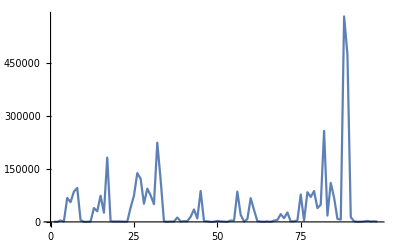

```mathematica
ListLinePlot[Map[Apply[LCM, #]&, Partition[RandomInteger[{1, 100}, 100], 3,1]], PlotRange->All]
```

In the same vein, plot the frequencies of the 100 possible two-digit pairs inside the first hundred thousand decimal digits of π. On average, each possible pair should occur roughly one thousand times, but in any random process there is always some inherent variance. (As an aside, the lack of such variance is how you recognize fake randomness generated by the human hand.)

-Graphics3D-

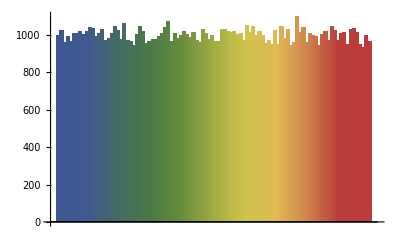

```mathematica
picounts = Tally[Partition[First[RealDigits[π, 10, 100000]], 2, 1]];
picounts = picounts /. {{x_, y_}, z_} -> {x, y, z};
ListPlot3D[picounts, Mesh->None,InterpolationOrder->0,Filling-> Axis, ColorFunction->"SouthwestColors"]
picounts = picounts /. {x_, y_, z_} -> {10*x + y, z};
picounts = Sort[picounts, (First[#1] < First[#2])&];
picounts = picounts /. {x_, y_} -> y;
BarChart[picounts, ChartStyle -> "DarkRainbow"]
```

The function GatherBy partitions the given list into a list of sublists, each sublist containing the equivalence class of the elements of the original list that evaluate to same result when applied to the function given to GatherBy as second argument. For example, separate the values in the list of integers depending on their modulus of 3.

```mathematica
GatherBy[Range[-10, 10], (Mod[#, 3])&]
```

{{-10,-7,-4,-1,2,5,8},{-9,-6,-3,0,3,6,9},{-8,-5,-2,1,4,7,10}}

For example, we can gather the first one million integers into separate sublists based on how many different prime factors they have. Since this list would be a wee bit too long to display comfortably, we shall rather render a mellow-looking bar chart of the results.

```mathematica
primefactored =GatherBy[Range[1, 10^6] ,(Length[FactorInteger[#]])&];BarChart3D[Map[Length, primefactored], ChartStyle-> "Pastel"]
```

-Graphics3D-

The particular calculation could also be done easier using the function Tally. Note the use of the substitution to project each element of the list produced by Tally, a list of two numbers for the element and its count in the original list, into its second element.

```mathematica
BarChart3D[Tally[Map[(Length[FactorInteger[#]])&,Range[1, 10^6]]] /. {elem_, count_} -> count, ChartStyle ->  "DeepSeaColors"]
```

-Graphics3D-

The function SplitBy is similar, but each list inside its result contains the run of consecutive elements of the original list that evaluate to the same result with respect to the function given as second argument. In the next example, group the numbers from 1 to 30 into sublists of consecutive numbers that are either all prime or all nonprime. (Of course, the only two consecutive integers that are prime numbers are 2 and 3.

```mathematica
SplitBy[Range[1, 30], PrimeQ]
```

{{1},{2,3},{4},{5},{6},{7},{8,9,10},{11},{12},{13},{14,15,16},{17},{18},{19},{20,21,22},{23},{24,25,26,27,28},{29},{30}}

The functions Append and Prepend tack a new element to the end and beginning of the list, respectively, producing new list for the result without modifying the original. Variants AppendTo and PrependTo are more imperative in spirit in that they modify the list that they operate on. It is important to understand that Append and Join, while seemingly similar, are not the same operation. This becomes evident by looking at the tree forms of their results when applied to the exact same arguments.

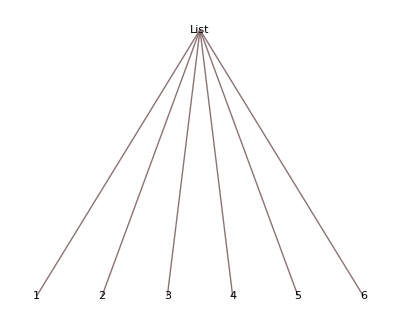
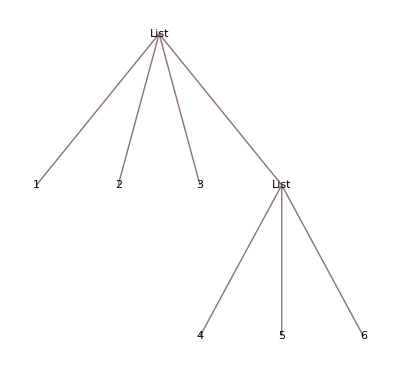

```mathematica
{TreeForm[Join[{1, 2, 3}, {4, 5, 6}]], TreeForm[Append[{1, 2, 3}, {4, 5, 6}]] }
```

The functions Union and Intersection sort both lists and produce the list that contains the elements in their union and intersection, respectively. For example, ignoring the meaning and pronunciation of each word and looking at only the letters that comprise it,what words are common to all four languages of English, French, German and Spanish?

```mathematica
Intersection[
Intersection[DictionaryLookup[{"English", All}], DictionaryLookup[{"French", All}]],
Intersection[DictionaryLookup[{"German", All}], DictionaryLookup[{"Spanish", All}]]
]
```

{adverbial,an,bar,bis,brutal,delta,diagonal,digital,es,fatal,final,frontal,global,gratis,horizontal,iota,man,marginal,monumental,nominal,normal,oh,pastoral,piano,plus,sentimental,territorial,total,trivial,verbal,vital}

Most of those words even mean the same thing in all four languages, seeing that these languages have influenced each other over the ages. On the other hand, how many words do these languages have when lumped all together?

```mathematica
Length[Union[DictionaryLookup[{"English", All}], DictionaryLookup[{"French", All}], DictionaryLookup[{"German", All}], DictionaryLookup[{"Spanish", All}]]]
```

383723

The function SubsetQ can be used to find out whether all elements of the second list are also elements of the first. If this function did not already exist, we could define it easily.

```mathematica
subsetQ[li1_, li2_] := Sort[li2] == Intersection[li2, li1];
subsetQ[Range[1, 10000, 2], Table[Prime[i], {i, 2, 100}]]
```

True

Alternatively, we could define this function using AllTrue and AnyTrue.

```mathematica
memberQ[li_, x_] := AnyTrue[li, (x == #)&];
subsetQ2[li1_, li2_] := AllTrue[li2, (memberQ[li1, #])&];
subsetQ2[Range[1, 10000, 2], Table[Prime[i], {i, 2, 100}]]
```

True

The functions Insert and Delete are used to add and remove elements to and from lists. Neither function modifies the original list, but produces a separate copy for the result. As with other list manipulation functions that behave this way, this is important to remember in the programs where the lists get huge, since each individual Insert or Delete ends up copying the entire underlying list every time.

```mathematica
mylist = {1, 2, 3, 4, 5}
mylist2 = Insert[mylist, "Hello world", 3];
mylist2
mylist
```

{1,2,3,4,5}

{1,2,Hello world,3,4,5}

{1,2,3,4,5}

To search for an element in the list, use the function Position. You can search for the occurrences of a literal element, or for an arbitrary pattern that can match many different elements. This function returns a part specification that you can use as index to access the elements that were found. Note that even for one-dimensional lists, each position is a list.

```mathematica
Position[{1, 2, 3, 4, 3, 2, 1}, 3]
```

{{3},{5}}

```mathematica
Position[{a^b, x, x^3, (z+1)^4}, b_^e_ ]
```

{{1},{3},{4}}

## Nesting and folding lists

After all these operations to create and modify lists of various sorts  it is time to use them to perform some interesting computations. In principle, all computation could be expressed as repeated and nested application of various decisions and repetitions. To choose between two possible alternatives, the function If evaluates either its second or third argument, depending on whether the first argument was True. This is similar to if-else in most other programming languages. Either argument can be a sequence of expressions separated by semicolons, which allows If to work for arbitrary bodies for both positive and negative branch.

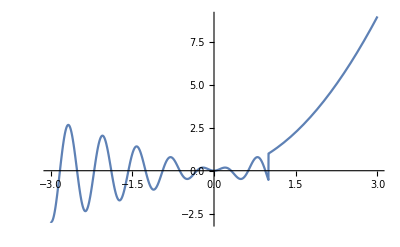

```mathematica
f[x_] := If[x<1, x Sin[10 x], x^2];
Plot[f[x], {x, -3, 3}]
```

As an aside, when defining actual mathematical functions, it is probably better to use Piecewise instead of If when a function is defined piecewise this way, so that the symbolic mathematics engine of Mathematica is able to handle it for functions such as integration. The result of some symbolic operation on a piecewise function is another piecewise function, unless the result happens to simplify into something prettier that is all in one piece. The Mathematica front end, of course, knows to display piecewise functions in the style that we are accustomed to in mathematical texts.

```mathematica
g[x_] := Piecewise[{{x Sin[10x], x < 1}, {x^2, x ≥ 1}}];
Integrate[g[x], x]
```

Piecewise[{{-1/10 x Cos[10 x]+1/100 Sin[10 x], x≤1}, {-1/3+x^3/3+1/100 (-10 Cos[10]+Sin[10]), True}}]

```mathematica
% // FullForm
```

Piecewise[List[List[Plus[Times[Rational[-1,10],x,Cos[Times[10,x]]],Times[Rational[1,100],Sin[Times[10,x]]]],LessEqual[x,1]]],Plus[Rational[-1,3],Times[Rational[1,3],Power[x,3]],Times[Rational[1,100],Plus[Times[-10,Cos[10]],Sin[10]]]]]

Our first way (with many more to come) to express repetition in Mathematica is by nesting a function by its repeated application starting from a seed value. The function Nest applies a function repeatedly the given number of times, whereas NestWhile applies the function as long as the result satisfies the condition gives as third parameter. Both functions produce only the last result of applying the function, so if you want the entire series of values along the way as the result list, use NestList or NestWhileList.

```mathematica
Nest[Function[x, x^2+1], 2, 5]
NestList[Function[x, x^2 + 1], 2, 5]
NestWhile[Sqrt, 10000, (#>2)&]
NestWhileList[Sqrt, 10000, (# > 2)&]
```

210066388901

{2,5,26,677,458330,210066388901}

10^(1/4)

{10000,100,10,√10,10^(1/4)}

The elements can, of course, be themselves arbitrary expressions, including lists.

```mathematica
msg = "Sator";
chars = NestList[RotateLeft,Characters[msg], StringLength[msg] - 1]; 
Grid[Map[Text[Style[#, FontSize -> RandomInteger[{20, 30}]]]&, chars, {2}]]
```

S | a | t | o | r
a | t | o | r | S
t | o | r | S | a
o | r | S | a | t
r | S | a | t | o

When the next element in the list depends only on the previous element that is passed as the argument to the function that is being nested, the nesting process is pretty straightforward.

```mathematica
Graphics[NestList[Translate[Rotate[#, π/11], {1, 0}]&, Line[ngon[5, 1]], 20] , ImageSize->Large]
```

-Graphics-

However, when additional information must ride along this nesting process, each element will have to be a list that contains several data values that all affect the computation of the next element. After NestList, use Map to project the result to consist only of only the things that you wanted, discarding all the auxiliary data values.

Many mathematical problems that don’t directly allow a closed form solution can be numerically estimated with statistical sampling in which a large number of samples from the problem domain are generated randomly, and the unknown quantity is estimated from the proportion of these random samples that satisfy this unknown quantity. A variation of a famous puzzle asks us to imagine a faraway country where the ruling sultan decrees that to maintain the institution of polygyny so that there would be at least “two girls for every boy” like in that Beach Boys song, every family must stop having any more children once they get a boy, reasoning that this will end up producing more girls and boys nationwide. Assuming that every family obeys this order, and boys and girls are equally likely to be born, what is the average proportion of boys and girls per family?

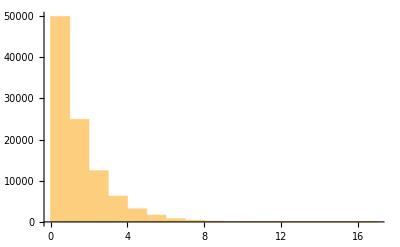

```mathematica
child := RandomChoice[{boy, girl}];
family := NestWhile[(#+1)&, 0,(child == girl)&];
Histogram[Table[family, {100000}]]
```

As you can see from the histogram, the number of girls in each family follows the geometric distribution over Bernoulli trials so that half of the families get zero girls before they get a boy, half of the remaining families get one girl, half of the remaining families get two girls, and so on. (This is the same distribution that you would get if you kept flipping a fair coin until you get heads.) The total number of boys and girls in the entire population is therefore not affected at all by the sultan’s decree, since each child has the same 50% probability of being a boy or a girl independent of other children that have come before or after him or her. So the sultan will just have to stick with the time-honoured solution of all polygynous societies for dealing with their surplus males by using them as cannon fodder instead.

But the original question was not about the intricacies of designing social policy in a kyriarchal despotism, but to compute the average proportion of boys to girls in each family. Note that the question says “proportion” that is computed by division, and division is not a linear function and therefore expected value does not obey the intuitively obvious but completely wrong formula. One might hastily conclude that since E[girls] = E[boys], then well, duh, obviously it must be that E[boys / (boys + girls)] = 1 / 2. But every time that you see the word “obviously” in a mathematical proof, let alone its even more “Shut up, he explained” spirited variation “It goes without saying that...”, that is always the first place to look for a swindle. Let us write a function sampler that is given the number of random samples to generate, and the function to combine the results with.

```mathematica
sampler[samples_, combine_] :=
Nest[Plus[#,combine[family]]&,0, samples] / samples;

N[sampler[1000000, (# / 2)&], 5]
N[sampler[1000000, (1/(1+#))&],5]
```

0.49915

0.69254

Even though the expected number of boys in each family equals the expected number of girls, it doesn’t follow at all that the the expected proportion boys / (boys + girls) would be even close to equal one half! In fact, this expected proportion is almost 70%. The fallacy involved in this modern day version of the famous Monty Hall puzzle stems from the misunderstanding of the behaviour of statistical expectation. The statistical expectation E of any distribution is a linear function over its arguments and therefore there is no denying that E[boys + girls] = E[boys] + E[girls], but linearity is not preserved over division, which is why E[boys / (boys + girls)] is generally not equal to E[boys] / E[boys + girls].

Don’t worry: many sharp minds have stumbled over this one. However, for those who insist that “The average number of boys per family equals the average number of girls per family, therefore when summed over all families, both numbers add up to same total, and therefore the expected proportion is 50%, because shut up”, pray tell, since you apparently believe that expectation is linear over division, surely you must then also believe that expectation is linear over multiplication, seeing that multiplication by a quantity equals the division by the inverse of that quantity? Do you believe that E[boys] * E[boys] = E[boys * boys]? In other words, do you believe that the variance of any data set or distribution is zero by definition?

Enough ranting. This problem does allow a symbolic solution for the expectation, showing that the true expectation for the proportion of boys in each family is Log[2]. This is close enough to the numerical approximation that we got above from our million random samples.

```mathematica
Sum[1/2^(k+1) * 1/(k+1), {k, 0, Infinity}] // FullSimplify
```

Log[2]

```mathematica
N[%, 5]
```

0.69315

Speaking of variance, defined in statistics as the average of the squares minus the square of average, we could compute that once using sampler. Or, simply calculate the Variance of the known distribution symbolically, but the idea was to practice using Nest and NestWhile. Even so, it is always reassuring to verify that symbolic formulas actually do refer to some phenomenon in reality so that we can then confidently use these formulas to predict this reality.

```mathematica
N[sampler[1000000, (#^2)&] - sampler[1000000, (#)&]^2]
Variance[GeometricDistribution[1/2]]
```

2.0223

2

In Nest and NestList, the function being nested could always just ignore the previous element that is given to it as argument, which would make the function NestList essentially behave as Table. Let us demonstrate this to estimate the probability that two randomly chosen integers are relatively prime, that is, their greatest common divisor equals one. Since it is impossible to choose a random integer from a uniform probability through all integers (since this set is infinite, the probability of each individual integer would be zero), we approximate this choice by choosing our random integers from the uniform distribution between one and one billion.

```mathematica
N[Total[NestList[Boole[GCD[RandomInteger[{1, 10^9}], RandomInteger[{1, 10^9}]] == 1]&,0, 1000000]] / 1000000, 5]
```

0.60754

Usually we think of π as this mysterious transcendental (in both the mathematical and everyday sense of this word) number that belongs to geometry, but should not have anything to do with integers or their primality. However, there is a surprising connection between the two in that the previous probability approaches 6 / π^2 as the range approaches infinity.

```mathematica
N[6 / (π^2), 5]
```

0.60793

Many computations can be expressed by nesting functions so that the seed value represents the initial state of some system, and the function that is repeatedly applied to it describes how the system develops in each single discrete time step, producing the next state of the system from the current state given to it as argument. In other words, this technique can be applied to generate a sequence of states of any Markovian system. (Nest can take an optional argument to tell it to consider the k previous elements instead of just one, but those systems are still Markovian with a state space whose size in general equals the k:th power of the original.)

Consider next Euclid, the ancient Greek who is best known for his axioms of planar geometry and the proof that there exist infinitely many prime numbers. Euclid also discovered the oldest nontrivial algorithm known in written history; the algorithm to find the greatest common divisor of two quantities. To find the greatest common divisor of two nonnegative integers a and b, calculate the remainder of the integer division a / b, and then calculate the greatest common divisor of b and this number. When b becomes zero, a contains the desired answer. Since the quantities strictly decrease in each step, the algorithm must eventually terminate. (Strictly speaking, Euclid’s original algorithm used subtraction a - b instead of remainder, which converges to the solution slower, but on the other hand, works not just for integers but also for line segments that are operated on geometrically.)

```mathematica
gcdstep[{a_, b_}] := If[a ≥ b,{b, Mod[a, b]}, {a, Mod[b, a]}];
gcd[a_, b_] := First[NestWhile[gcdstep, {a, b}, (#[[2]] > 0)&]];
gcd[123456, 654321]
```

3

Mathematica has the built-in function GCD that does the job quickly even for humongous numbers, since doubling the magnitude of the arguments adds only a constant to the running time of this algorithm. (The running time of algorithms that behave this way is logarithmic with respect to their input. However, if the size of the input is measured in how many digits comprise the number instead of the absolute magnitude of that number, the algorithm takes linear time to compute the GCD.)

```mathematica
GCD[BellB[1000], StirlingS2[1000, 491]]
```

7

To sink our teeth into a sinewy integer problem from more current times, consider the Collatz problem, a famous mathematical problem that is simple enough that it could be explained to and understood by the average ten-year-old, but yet somehow still remains unsolved to this day, eluding the powers of even the finest white gentlemen and officers diligently working in the service of Her Majesty, their magnificient wits aided by our mightiest calculation machines powered by steam. Starting from some given positive integer, the Collatz sequence is defined with two simple rules that involve only basic arithmetic. If the current number is odd, the next number is computed by multiplying the current number by three and adding 1. If the current number is even, the next number is computed by dividing the current number by two. Keep producing this sequence until the number becomes 1.

```mathematica
collatzstep[x_]:=If[EvenQ[x],x/2,3*x+1];
collatzSeries[x_]:=NestWhileList[collatzstep,x,(#>1)&];
```

When started from different seed numbers, the sequence bounces up and down seemingly randomly, which is why this sequence is also known as the “hailstone sequence”. For some starting values, the sequence will take a surprisingly long time to reach the goal state of value one. Of course, as soon as the current value becomes some power of two, its repeated division by two will quickly set the series to a deep dive towards the goal.

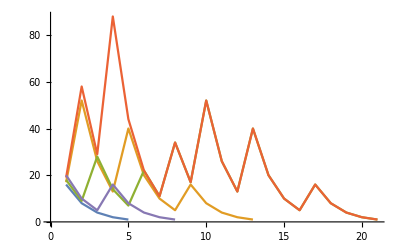

```mathematica
ListLinePlot[Table[collatzSeries[start], {start, 16, 20}]]
```

The unsolved problem about these sequences is to prove whether this sequence will always eventually reach the value 1, regardless of your choice of the starting value. This has been numerically verified up to very large numbers, but nobody has been able to come up with a general proof that would apply to all positive integers, and in the absense of such proof, infinitely many starting numbers will always remain unverified, so the counterexample could always be lurking just behind the corner after the highest value has been verified so far. When we plot the number of steps it takes to reach the goal value from different starting values from 1 to 20000, the plot does indeed display some sort of regularity, but how this pattern continues towards infinity, nobody knows. There seems to be a pretty pattern emerging in the following ListPlot, though.

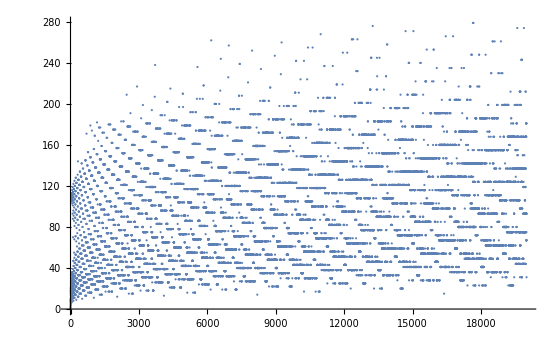

```mathematica
ListPlot[Table[Length[collatzSeries[i]],{i,1,20000}]]
```

We can also plot the maximum values reached during the iteration, shown here for each starting value from 1 to 20000. Some starting values get up pretty high before converging to the goal. Since the Collatz series from many starting numbers meet in some number and continue identically from there, same maximum numbers reached tend to repeat for multiple starting points.

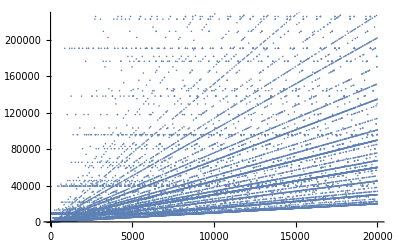

```mathematica
ListPlot[Table[Max[collatzSeries[i]],{i,1,20000}]]
```

Collatz sequences can also be expressed as a list of substitutions that together produce a directed graph. This graph is infinite, so we shall just look at the first fifty elements. As you included more elements in the graph, the separate disconnected components would eventually connect with each other.

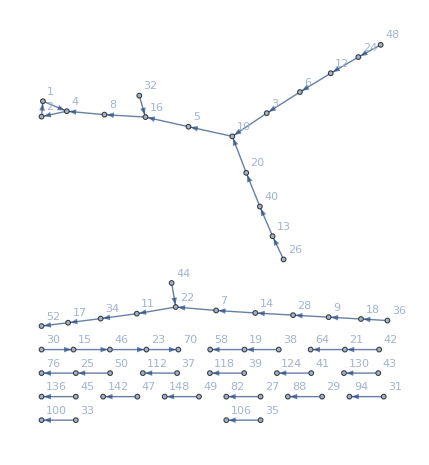

```mathematica
Graph[Map[(#1 -> collatzstep[#1])&, Range[1, 50]], VertexLabels ->"Name"]
```

We shall leave the intricacies of the Collatz problem to smarter people who work above our pay grade, and think about reaching infinity another way. Another mathematical thingamagic, Knuth’s uparrow notation is used to express numbers so huge that they make mere astronomical numbers feel like you could practically count them with your fingers and toes. Be very careful before attempting to explicitly compute these towers upon towers of exponents that boldly rise to almost scrape the nose of the infinity itself.

```mathematica
UpArrow[a_,n_Integer]:=Nest[a^#&,1,n];
Table[UpArrow[x, i], {i, 1, 5}]
```

{x,x^x,x^(x^x),x^(x^(x^x)),x^(x^(x^(x^x)))}

Let us tabulate some concrete values of i ↑ j for a couple of small values of i and j.

```mathematica
Table[N[UpArrow[i,j]], {i, 1, 6}, {j, 1, 3}] // MatrixForm
```

(1. | 1. | 1.
2. | 4. | 16.
3. | 27. | 7.6256×10^12
4. | 256. | 1.34078×10^154
5. | 3125. | 1.91101259794548×10^2184
6. | 46656. | 2.65911977215323×10^36305)

There is a very good reason why we didn’t even try to include the fourth column in that matrix. And anyway, this is only the first uparrow. The second uparrow would produce a tower of exponents whose height is given by the first uparrow. (Read that sentence again and think about it for a moment.) The third uparrow would create a tower of exponents whose height is given by the second uparrow, and so on. The Ackermann function A(k) can be concisely defined as application of a total of k uparrows to the parameter k, the seemingly innocent definition unleashing a monster that grows so fast that it actually breaks through the boundaries of primitive recursive computability itself. (A function is primitive recursive if it can be computed by using some fixed series of sequential and nested for-loops so that modifying the loop counter or the termination target inside the loop body is forbidden. The Ackermann function cannot be computed this way, but necessarily needs an unlimited while-loop to be computed. But only in principle, of course.)

It’s getting dizzy up there in the mathematical heights, so we must return to the cozy confines of the Earth. Random walks seem to be pretty standard examples of iteration with Mathematica. Proceeding from the given starting point, take one step at a time to a randomly chosen direction. Repeat this a large number of times and, and plot the positions that you visited along the way. First, a one-dimensional random walk with unit steps. One might intuitively expect this walk to remain near the zero seeing that moves to both directions are equally likely, but to correct a common misconception about how randomness behaves in the long run, luck doesn’t somehow magically “even out” over time in the long run, even in that run beloved by Keynesians that is so long that we are all dead by then. The proportion of moves going up and down does indeed approach 1 as time increases, as seen in the red curve in the plot below even when multiplied by 100 to make it more visible, but the absolute difference between the ups and downs in the random walk will only grow ever larger with probability 1.

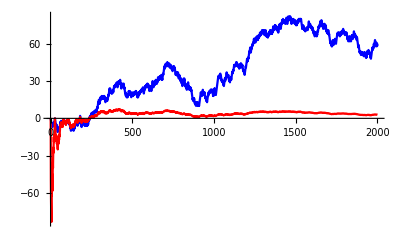

```mathematica
step[x_] := x + RandomChoice[{-1, +1}];
walk1d = NestList[step, 0,2000];
walkprop = MapIndexed[(#1/#2)&, walk1d] /. {x_} -> 100 x;
ListLinePlot[{walk1d, walkprop}, PlotStyle -> {Blue, Red}]
```

The next example illustrates a two-dimensional random walk with the step size d drawn from the exponential distribution, and the step angle ϕ drawn from uniform distribution of the possible angles. (Choosing the step size separately for x and y would bias the directions disproportionately away from the main compass directions.) The handy function With can be used to simplify complicated expressions that need the result of some subexpression several times, so we would prefer not to compute that subexpression again each time. The first argument of With is a list a symbolic assignments that define the local constants for the expression given as second argument. In the next example of random walk, we want the random value of ϕ to be the same in both subexpressions with the sine and cosine, so With is used first to set the value of ϕ in stone for that particular step. With is similar to Module in the sense that the symbols defined in it are local and thus cannot accidentally redefine any globally defined symbols. Here is a simulation of Brownian motion where each step is taken to a random direction chosen uniformly from the entire 360 degrees.

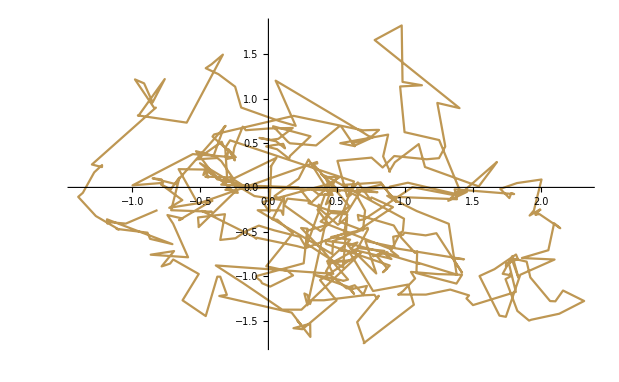

```mathematica
step[{x_, y_}] := With[
{ϕ = RandomReal[2*π], d = RandomVariate[ExponentialDistribution[5]]}, { x +d * Sin[ϕ], y + d*Cos[ϕ] }
];
ListLinePlot[NestList[step, {0, 0}, 500], ColorFunction -> "SouthwestColors"]
```

Nest and its variations can be used to compute sequences where you are given exactly one starting value, and the next value in the sequence depends only on the current value. The function Fold works the opposite way in the sense that you start with a full list of values and an additional seed value, which is the initial state of your computation to “prime the pump”, so to speak. The iteration of Fold proceeds by applying the given two-parameter function to the current state and the next value of the list, and the result then becomes the new current state of your computation. When all the values in the list have been processed this way, the final state of this iteration is returned as the result. FoldList does the same computation, but analogously to NestList, produces the list of all intermediate results instead of just the final result.

```mathematica
Fold[(#1 + Sin[#2])&, x, {a, b, c}]
FoldList[(#1 + Sin[#2])&, x, {a, b, c}]
```

x+Sin[a]+Sin[b]+Sin[c]

{x,x+Sin[a],x+Sin[a]+Sin[b],x+Sin[a]+Sin[b]+Sin[c]}

As we saw in an earlier example, Mathematica already has the built-in function Harmonic to calculate harmonic numbers (the k:th harmonic number H_k is defined to be equal to the sum of reciprocals of the first k integers), but even if it didn’t, the harmonic numbers would be easy to compute with folding. To make this more dynamic and interesting, let us illustrate the effect of Manipulate to allow the user to interactively choose which power to use.

```mathematica
Manipulate[ListLinePlot[FoldList[(#1 + 1/#2^exp)&, 0, Range[1, 200]]], {exp, 0.2, 2, 0.1}]
```

The predefined function Total adds up the elements of its parameter list and evaluates to the total. (If you want to produce the list of all intermediate values instead of just the grand total in the end, use the function Accumulate.) Should we pretend for a moment that this immensely useful function didn’t exist for some reason, it would also be quite easy to define using Fold. The initial state of folding when nothing has yet been added is zero. The function that we provide as the first argument takes the current state and adds the next element of the list to it, producing the next state.

```mathematica
Total[{a, 2, x^7, foobar}]
Fold[Plus, 0, {a, 2, x^7, foobar}]
```

2+a+foobar+x^7

2+a+foobar+x^7

Once again, harmonic numbers famously do not converge, but reach ever higher values as n approached infinity. But what if we left out some terms to hinder this growth, such as each term whose denominator contains the digit 9 somewhere in it? Such a horrendous problem more suited for the brain of Ramanujan at least lets us graph the evolution of this sum and see which way it seems to be converging.

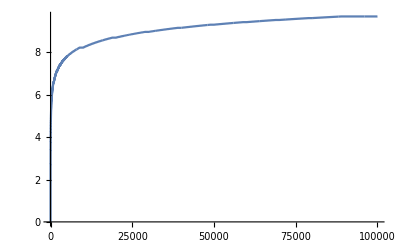

```mathematica
kempner[n_] := FoldList[(If[MemberQ[IntegerDigits[#2], 9], #1, #1+1/#2])&, 0, Range[1,n]];
ListLinePlot[kempner[100000]]
```

The next example generates a two-dimensional random walk restricted to unit steps to the four main compass directions. The initial state is the origin (0, 0), and the next state is generated by taking the next element of the list of random direction offsets and taking a step to that direction. The list dirs contains the direction offsets for each of the four possible directions of movement, that is, the values to add to the current x and y coordinates. The function RandomChoice is used to generate a list of 1000 randomly chosen direction offsets with replacement, since of course we should be able to move to the same direction many times.

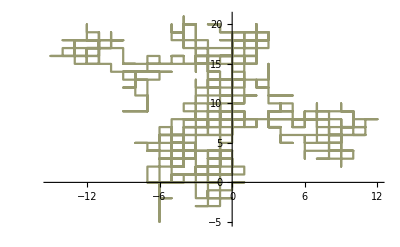

```mathematica
dirs = { {0, 1}, {1, 0}, {-1, 0}, {0, -1} };
ListLinePlot[FoldList[Plus, {0, 0}, RandomChoice[dirs, 1000]], ColorFunction-> "Rainbow"]
```

Instead of using a list of randomly chosen directions, we could express some decimal number in base 4 and use its digits to determine the direction in each step. The handy functions IntegerDigits and RealDigits can convert any number into a list of digits in any base. Since there are four directions to move to randomly and ten is not divisible by four, we extract the digits of the number in base four. As the possible digits in base 4 are 0, 1, 2 and 3, we need to add one to these to be able to use them as list indices to the direction offsets list. Like many functions in Mathematica, Plus is Listable so that adding a scalar value to a list simply adds that scalar separately to each element of the list.

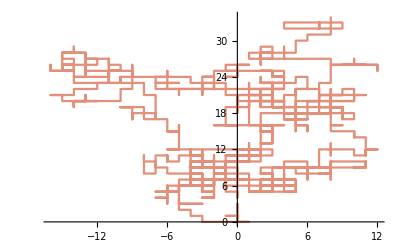

```mathematica
numberwalk[x_] := FoldList[Plus, {0, 0},Map[(dirs[[#+1]])&, First[RealDigits[x, 4, 1000, -1]]]];
ListLinePlot[numberwalk[π], ColorFunction->Function[{x, y}, RGBColor[Mod[x+y, 2], x, y]]]
```

Different numbers produce different walks. However, for any rational number, this walk by definition soon becomes periodic and thus rather boring. Irrational numbers produce more interesting fractal walks.

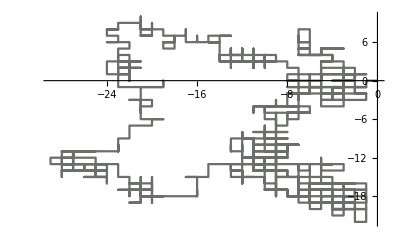

```mathematica
ListLinePlot[numberwalk[Sqrt[3]], ColorFunction ->"DarkTerrain"]
```

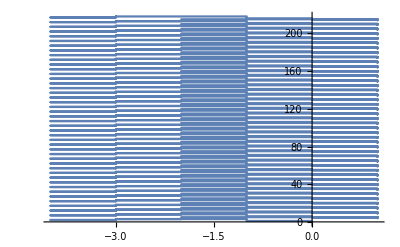

```mathematica
ListLinePlot[numberwalk[6/47]]
```

## Additional examples of list manipulations

The next example will generate a hundred random points on the plane, calculate their pairwise distances and plot them in sorted ascending order, leaving out the zero distances of each point with itself. Finally, display a histogram of these distances, sorted into ten separate bins.

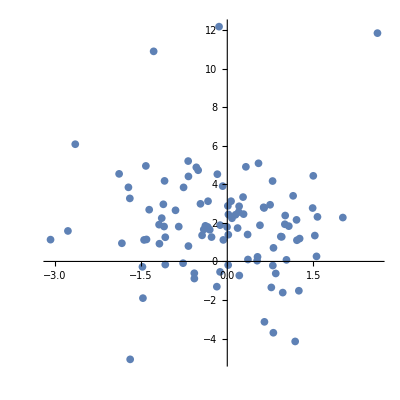

```mathematica
points = Table[{RandomVariate[NormalDistribution[0, 1]], RandomVariate[LaplaceDistribution[2, 2]]}, {i, 1, 100}];
ListPlot[points, AspectRatio -> 1]
```

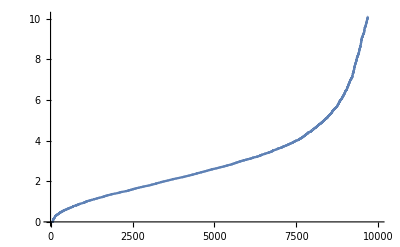

```mathematica
distances = Map[(EuclideanDistance[#[[1]], #[[2]]])&, Tuples[points, 2]];
distances = Drop[Sort[distances], 30];
ListLinePlot[distances]
```

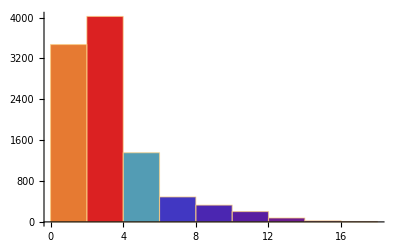

```mathematica
Histogram[distances, 10, ColorFunction -> "Rainbow"]
```

Speaking of Listable functions, being Listable is one of the many attributes that the functions can have. To make your own function Listable, simply set that attribute to be on for that function. When applied to a list, a Listable function is applied to the elements of that list, whereas a function that is not listable is applied to the entire list at once.

```mathematica
fun1[x_] := {x, x+1};
fun2[x_] := {x, x+1};
SetAttributes[fun2, Listable];
fun1[{1, 2, 3}]
fun2[{1, 2, 3}]
```

{{1,2,3},{2,3,4}}

{{1,2},{2,3},{3,4}}

When applied to anything that is not a list, there is no difference in the behaviour of these two functions.

```mathematica
fun1[3]
fun2[3]
```

{3,4}

{3,4}

Listable functions save us the drugdery of having to write the code to iterate some function over the elements of some list.

```mathematica
PrimeQ[Range[10, 20]]
```

{False,True,False,True,False,False,False,True,False,True,False}

```mathematica
Map[PrimeQ, Range[10, 20]]
```

{False,True,False,True,False,False,False,True,False,True,False}

All of Mathematica’s built-in arithmetic is listable.

```mathematica
1/ { {2, 2 + {1,2,3,4}}, {3, 3, 3*{5,6,7}} }
```

{{1/2,{1/3,1/4,1/5,1/6}},{1/3,1/3,{1/15,1/18,1/21}}}

The symbolic computation of Mathematica can operate on complex numbers with the imaginary unit built in the language as the constant I. Real numbers are a trivial special case of complex numbers with a zero imaginary part, which causes the arithmetic operations on real numbers to remain on the real line, until you divide by zero or try to extract the square root of a negative number. Many numerical and symbolic algorithms of Mathematica can optionally be restricted to either Complex domain, or the analogous extension of integers, Gaussian integers that are complex numbers whose both real and imaginary components are integers. The functions Re and Im extract the real and imaginary parts of a complex number, whereas Abs and Arg extract its absolute value and polar angle. The next illustrative example adapted from the page “Circle Squares Fractal” in Paul Bourke’s excellent fractal art site. Each pixel is treated as a complex number that is first squared and the result is taken modulo m. As we plot the operation for various m, different interference patterns emerge.

```mathematica
compmod[z_, m_] := Mod[Abs[z], m]*(Re[z]+Im[z] I)/ Abs[z];
cmod[m_, wx_, wy_] := Table[compmod[(x+y I)*(x+y I), m], {x, 1, wx}, {y, 1, wy}];
GraphicsGrid[Partition[Table[ArrayPlot[cmod[m, 40, 40]], {m, 1, 40}], 8]]
```

-Graphics-

Even though Mathematica comes with not just the single step iteration functions MandelbrotSetIterationCount and MandelbrotSetMemberQ but also the full MandelbrotSetPlot built in the language, it is always a good and healthy exercise to write this plot function ourselves. This will also allow us to experiment with exponents other than 2, and observe their effects on the shape of the set that is otherwise quite familiar, or at least it was during the heyday of fractals in the early nineties, after which all these fractal shape somehow quietly vanished from our cultural consciousness. Note that the use of negative or non-integer exponents would slow down this computation quite a bit.

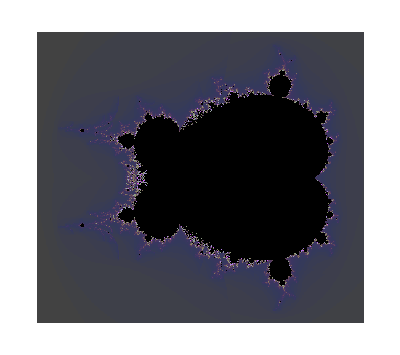

```mathematica
mandel[top_, exp_, res_, px_, py_,escape_, maxiter_] := 
Table[
With[{cp = (top + (x res - (y res) I))},
Length[NestWhileList[(#^exp + cp)&, cp, (Abs[#] < escape)&, 1, maxiter]]
], {y, 0, py-1}, {x, 0, px-1}];

mp = ArrayPlot[mandel[-2 + 1.2I, 2.1, 2.4 / 400, 450, 400, 2, 100], ColorRules -> {101 -> Black}, ColorFunction -> "AuroraColors"]
```

Image processing algorithms can be used to examine the resulting images. The function Rasterize can take any expression, including but not limited to Graphics, and turn it into a pixel image, which can then be passed on to the image processing functions. The rasterization process can be performed with an arbitrary size and resolution.

```mathematica
Table[ImageResize[Rasterize[mp,"Image",RasterSize -> r^2], 150],{r, 4, 18,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Mathematica comes with a powerful set of Photoshop-style functions for all imaginable sorts of image analysis and transformation operators, and since the power of universal algorithm computation is added on top of them, all kinds of cool things can be done with just a couple of lines of code. Since images are expressions (well yes, of course they are very long and complicated expressions, but expressions nonetheless, and unlike we humans, the computer doesn’t care even if some expression is a million bytes long, but chomps it down one byte at the time without one sideways word of attitude or complaint), so we can make lists of images, and lists of lists that contain images, and so on to the smallest whorls and fleas, and then manipulate all these lists computationally to our hearts content.

```mathematica
WatershedComponents[Rasterize[mp,"Image",ImageResolution->72]] // Colorize
```

-Graphics-

Generalizing even higher up from the complex numbers, Mathematica even supports quaternions. Quaternions are a generalization of complex numbers by using three imaginary components I, J and K instead of just one such component, at the cost that multiplication no longer being noncommutative, that is, the product (a*b)*c in general is not equal to the product a*(b*c). So that Mathematica does not try to simplify expressions involving multiplications of quaternions wrongly assuming commutativity, you can use the noncommutative multiplication operator ** where the asterisk is duplicated. This operator behaves otherwise exactly like multiplication, except that Mathematica will not assume that this operator is commutative when it simplifies the expressions that use it. (For the same reason, Mathematica does not use the symbol + for string concatenation, but an entirely different operator symbol <> instead, because string concatenation is not commutative.) 

As large as Mathematica is, it still can’t possibly include every possible mathematical function or algorithm. To allow the language to be extended, definitions can be stored in packages. The package is read in the kernel with the function Needs, after which the functions defined in that package look and behave just like other Mathematica functions. The package also adds rules concerning the existing functions such as Abs so that they know to work correctly with the new data type. Since this lesson is about lists and tables, we might as well use Mathematica to generate and display the multiplication table for the sixteen combinations of the real and imaginary unit components of quaternions.

```mathematica
Needs["Quaternions`"];
units = Table[FromQuaternion[RotateRight[Quaternion[1,0,0,0], k]], {k, 0, 3}];
qmt = Table[units[[i]]*units[[j]], {i, 1, 4}, {j, 1, 4}];
TableForm[qmt, TableHeadings -> {units, units}]
```

| 1 | ⅈ | J | K
1 | 1 | ⅈ | J | K
ⅈ | ⅈ | -1 | ⅈ J | ⅈ K
J | J | ⅈ J | J^2 | J K
K | K | ⅈ K | J K | K^2

Quaternions have surprising applications, most importantly in the smooth interpolation of position over time over spherical surfaces so that the velocity remains constant throughout... but suddenly, a wild mandrill appears!

```mathematica
mandrill = ImageResize[ExampleData[{"TestImage","Mandrill"}], 300]
```

-Graphics-

With image processing, we can tame this savage beast a bit and make him do all kinds of tricks for us. He doesn’t seem so dangerous any more. Nice monkey!

```mathematica
Grid[{
{Erosion[mandrill, 3], Dilation[mandrill, 3],ColorNegate[mandrill]}, {BottomHatTransform[mandrill,3], Closing[mandrill, 6], Opening[mandrill, DiamondMatrix[20]]}
}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Here is a cool little Mathematica trick taken from the blog “Lunchtime Playground”. Looking only at brightness and ignoring the other aspects of the colour of each pixel, each row of the image is treated a list of values, which can then be plotted with ListPlot like any other list. Plot a whole bunch of these rows in the same plot, and the result is fit for the cover of some Joy Division album. Confusion in its eyes that says it all.

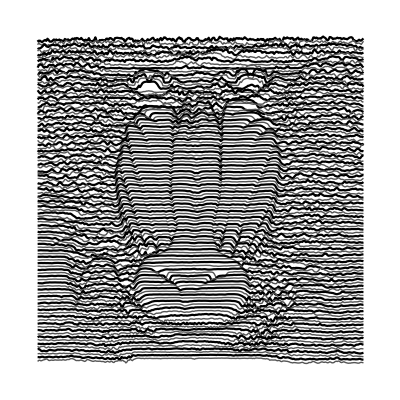

```mathematica
imgb=ImageData[ColorConvert[mandrill,"HSB"]][[All,All,3]];
ListPlot[Table[imgb[[i]]*10-i,{i,1,ImageDimensions[mandrill][[2]],3}],PlotRange->All,Axes->None,Joined->True,PlotStyle->{{Black},{Thick,Lighter[Black]}},AspectRatio->ImageAspectRatio[mandrill]]
```

The CountryData knowledge base contains entities representing all the nations in the world, and one of the properties of those entities is their flag images, of which here we display a small initial sample. How many of these can you name offhand without googling? (Hint: the countries come sorted alphabetically by name.)

```mathematica
flags = Map[RemoveAlphaChannel[ImageResize[CountryData[#, "Flag"], {20, 20}]]&, CountryData[]];
Take[flags, 15]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The function ImageData (which, despite the suggestive name, is not any of Mathematica’s built-in knowledge bases) turns an image into a three-dimensional list of the RGB colour components of each pixel. Here is the first row of pixels of the first flag in our list, just to illustrate what is going on in here. The first five pixels are all black, as can be seen from how all three of their colour components are zero.

```mathematica
Take[ImageData[flags[[1]]], 1]
```

{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.00784314,0.,0.},{0.294118,0.,0.},{0.717647,0.,0.},{0.74902,0.,0.},{0.74902,0.,0.},{0.74902,0.,0.},{0.74902,0.,0.},{0.705882,0.0352941,0.},{0.247059,0.4,0.},{0.00392157,0.596078,0.},{0.,0.6,0.},{0.,0.6,0.},{0.,0.6,0.},{0.,0.6,0.},{0.,0.6,0.}}}

Using Map and Flatten, we can write a function that, given the ImageData of some image as its first argument, finds the flag whose difference to that image is the minimum. The function Ordering, when applied to a list and a position, returns the current position of the element that would end up in the given position if the list were sorted. This function is the handy way to compute various order statistics of the list such as minimum, maximum or median without first having to sort the list. Using position argument 1 is therefore equivalent to asking for the minimum element of the list, but with this function, you could look for the median element, the element at the sixth decile, or any order statistic whatsoever that you were interested in.

```mathematica
closest[imgd_, list_] := list[[Ordering[Map[Total[Abs[Flatten[imgd - ImageData[#]]]]&, list], 1]]];
```

Armed with this function, it is now almost hilariously trivial to implement the classic photomosaic algorithm that replaces each piece of the given image by the flag that most resembles that piece, as measured with the total sum of pixel colour differences over the image. The image that is turned into a mosaic is first partitioned into a table of images the same size as the tile images that are used to fill in this mosaic, and each smaller image is replaced by whichever one of these tile images is visually closest to it. The function ImageAssemble is then used to combine these images back to a single image.

```mathematica
mosaic[img_] := Module[{pieces},
pieces = ImagePartition[img, 20];
ImageAssemble[Map[First[closest[ImageData[#], flags]]&, pieces, {2}]]
];
GraphicsGrid[{{mandrill, mosaic[mandrill]}}]
```

-Graphics-

Flags of countries tend to be flat and uniform pretty much by design as to make them identifiable from distance, so the results immediately bring to mind the blocky 8-bit graphics of the good old Sinclair ZX Spectrum where each 8-by-8 block of pixels, normally used to show one character on its 256-by-192 pixel screen, could have exactly one background colour and exactly one foreground colour, regardless of the particular pixels that were turned on or off in that cell, resulting in the ugly computer graphics colour bleeding phenomenon known as attribute clash. Using more colourful and varied images instead of flags would then produce smoother image mosaics. But to close off this document, here are a couple more test images turned into mosaics of country flags, just for the kicks.

```mathematica
images = Map[ImageResize[ExampleData[{"TestImage", #}], 240]&, {"House2", "Girl3", "Splash", "Flower", "Girl", "JellyBeans", "Couple", "Airplane2", "Man", "Peppers"}];
GraphicsGrid[Partition[Flatten[Map[{#, mosaic[#]}&, images]], 4]]
```

-Graphics-